In this note book the Vector tools by Dr. Alan A Barhorst was used. Please contact him via alan.barhorst@louisiana.edu for it. 
You can cite the work of this notebook using: 
Amarasiri, N., Barhorst, A. A., and Gottumukkala, R. (March 7, 2024). “Investigating Suitable Combinations of Dynamic Models and Control Techniques for Offline Reinforcement Learning Based Navigation: Application of Universal Omni-Wheeled Robots.” ASME. Letters Dyn. Sys. Control. April 2024; 4(2): 021007. https://doi.org/10.1115/1.4064517

This paper can be downloaded using https://www.researchgate.net/profile/Nalaka-Amarasiri

Please cite the vector tools by using:
Barhorst, A. A., 1997, “Symbolic Equation Processing Utilizing Vector/Dyad Notation,” J. Sound Vib., 208(5), pp. 823–839.

## Please copy Omni_robot _Generalized _momenta _Dynamics _PID _Part _ 1 and Omni_robot _Generalized _momenta _Dynamics _PID _Part _ 2 here to run the PID Controller

## PID Controller

#### Clearing variables

First clear all the variables of the kinematics.  Sometimes this may cause an error if they have not been assigned numbers yet. Ignore the error and proceed.

```mathematica
Subscript[q, 1][t_]=.;
Subscript[q, 2][t_]=.;
Subscript[q, 3][t_]=.;
Subscript[q, 4][t_]=.;
Subscript[q, 5][t_]=.;
Subscript[q, 6][t_]=.;
Subscript[q, 7][t_]=.;
Subscript[q, 8][t_]=.;
Subscript[q, 9][t_]=.;
Subscript[q, 10][t_]=.;
Subscript[q, 11][t_]=.;
Subscript[q, 1]'[t_]=.;
Subscript[q, 2]'[t_]=.;
Subscript[q, 3]'[t_]=.;
Subscript[q, 4]'[t_]=.;
Subscript[q, 5]'[t_]=.;
Subscript[q, 6]'[t_]=.;
Subscript[q, 7]'[t_]=.;
Subscript[q, 8]'[t_]=.;
Subscript[q, 9]'[t_]=.;
Subscript[q, 10]'[t_]=.;
Subscript[q, 11]'[t_]=.;
Subscript[q, 1]''[t_]=.;
Subscript[q, 2]''[t_]=.;
Subscript[q, 3]''[t_]=.;
Subscript[q, 4]''[t_]=.;
Subscript[q, 5]''[t_]=.;
Subscript[q, 6]''[t_]=.;
Subscript[q, 7]''[t_]=.;
Subscript[q, 8]''[t_]=.;
Subscript[q, 9]''[t_]=.;
Subscript[q, 10]''[t_]=.;
Subscript[q, 11]''[t_]=.;
Subscript[Q, 1][t_]=.;
Subscript[Q, 2][t_]=.;
Subscript[Q, 3][t_]=.;
Subscript[Q, 4][t_]=.;
Subscript[Q, 5][t_]=.;
Subscript[Q, 6][t_]=.;
Subscript[Q, 7][t_]=.;
Subscript[Q, 8][t_]=.;
Subscript[Q, 9][t_]=.;
Subscript[Q, 10][t_]=.;
Subscript[Q, 11][t_]=.;
Subscript[ω, 1][t_]=.;
Subscript[ω, 2][t_]=.;
Subscript[ω, 3][t_]=.;
Subscript[ω, 4][t_]=.;
ω=.;
A=.;
B=.;
Cc=.;
r=.;
R=.;
t=.;
Ω=.;
A1=.;
A2=.;
A3=.;
A4=.;
A6=.;
A8=.;
A10=.;
B4=.;
B6=.;
B8=.;
B10=.;
b4=.;
b6=.;
b8=.;
b10=.;
p4[t_]=.;
p6 [t_]=.;
p8[t_]=.;
p10[t_]=.;
p4'[t_]=.;
p6 '[t_]=.;
p8'[t_]=.;
p10'[t_]=.;
p4=.;
p6 =.;
p8=.;
p10=.;
q1[t_]=.;
q2[t_]=.;
q3[t_]=.;
q4[t_]=.;
q5[t_]=.;
q6[t_]=.;
q7[t_]=.;
q8[t_]=.;
q9[t_]=.;
q10[t_]=.;
q11[t_]=.;
Tmot[1]=.;
Tmot[2]=.;
Tmot[3]=.;
Tmot[4]=.;
Subscript[Tmot, 1][t]=.;
{{Subscript[Tmot, 2][t]=.;}, {Subscript[Tmot, 3][t]=.;
Subscript[Tmot, 4][t]=.;}}
```

Unset::norep: Assignment on Derivative for q_1'[t_] not found.

Unset::norep: Assignment on Derivative for q_2'[t_] not found.

Unset::norep: Assignment on Derivative for q_3'[t_] not found.

Unset::norep: Assignment on Derivative for q_4'[t_] not found.

Unset::norep: Assignment on Derivative for q_5'[t_] not found.

Unset::norep: Assignment on Derivative for q_6'[t_] not found.

Unset::norep: Assignment on Derivative for q_7'[t_] not found.

Unset::norep: Assignment on Derivative for q_8'[t_] not found.

Unset::norep: Assignment on Derivative for q_9'[t_] not found.

Unset::norep: Assignment on Derivative for q_10'[t_] not found.

Unset::norep: Assignment on Derivative for q_11'[t_] not found.

Unset::norep: Assignment on Derivative for q_1''[t_] not found.

Unset::norep: Assignment on Derivative for q_2''[t_] not found.

Unset::norep: Assignment on Derivative for q_3''[t_] not found.

Unset::norep: Assignment on Derivative for q_4''[t_] not found.

Unset::norep: Assignment on Derivative for q_5''[t_] not found.

Unset::norep: Assignment on Derivative for q_6''[t_] not found.

Unset::norep: Assignment on Derivative for q_7''[t_] not found.

Unset::norep: Assignment on Derivative for q_8''[t_] not found.

Unset::norep: Assignment on Derivative for q_9''[t_] not found.

Unset::norep: Assignment on Derivative for q_10''[t_] not found.

Unset::norep: Assignment on Derivative for q_11''[t_] not found.

Unset::norep: Assignment on Subscript for Q_1[t_] not found.

Unset::norep: Assignment on Subscript for Q_2[t_] not found.

Unset::norep: Assignment on Subscript for Q_3[t_] not found.

Unset::norep: Assignment on Subscript for Q_4[t_] not found.

Unset::norep: Assignment on Subscript for Q_5[t_] not found.

Unset::norep: Assignment on Subscript for Q_6[t_] not found.

Unset::norep: Assignment on Subscript for Q_7[t_] not found.

Unset::norep: Assignment on Subscript for Q_8[t_] not found.

Unset::norep: Assignment on Subscript for Q_9[t_] not found.

Unset::norep: Assignment on Subscript for Q_10[t_] not found.

Unset::norep: Assignment on Subscript for Q_11[t_] not found.

Unset::norep: Assignment on Subscript for ω_1[t_] not found.

Unset::norep: Assignment on Subscript for ω_2[t_] not found.

Unset::norep: Assignment on Subscript for ω_3[t_] not found.

Unset::norep: Assignment on Subscript for ω_4[t_] not found.

Unset::norep: Assignment on Derivative for p4'[t_] not found.

Unset::norep: Assignment on Derivative for p6'[t_] not found.

Unset::norep: Assignment on Derivative for p8'[t_] not found.

Unset::norep: Assignment on Derivative for p10'[t_] not found.

Unset::norep: Assignment on Subscript for Tmot_1[t] not found.

Unset::norep: Assignment on Subscript for Tmot_2[t] not found.

Unset::norep: Assignment on Subscript for Tmot_3[t] not found.

Unset::norep: Assignment on Subscript for Tmot_4[t] not found.

General::stop: Further output of Unset::norep will be suppressed during this calculation.

{{Null},{Null^2}}

```mathematica
Subscript[q, 4]'[t]=.;
Subscript[q, 6]'[t]=.;
Subscript[q, 8]'[t]=.;
Subscript[q, 10]'[t]=.;
p4'[t]=.;
p6'[t]=.;
p8'[t]=.;
p10'[t]=.;
```

Unset::norep: Assignment on Derivative for q_4'[t] not found.

Unset::norep: Assignment on Derivative for q_6'[t] not found.

Unset::norep: Assignment on Derivative for q_8'[t] not found.

Unset::norep: Assignment on Derivative for q_10'[t] not found.

Unset::norep: Assignment on Derivative for p4'[t] not found.

Unset::norep: Assignment on Derivative for p6'[t] not found.

Unset::norep: Assignment on Derivative for p8'[t] not found.

Unset::norep: Assignment on Derivative for p10'[t] not found.

### Formulating control equations

eom1, eom2, eom3, eom4 --> These are momentum equations f(q_j, p_k, u_l) Here u_l is the Tmot[i].
eom5, eom6, eom7, eom8, eom9, eom10, eom11, eom12, eom13, eom14, eom15 --> These are kinematic equations g(q_(j,)p_k)

Let’s make control equations using PID gains

#### Control laws and control equations of motion

Clear everything again.

```mathematica
Tmot[1]=.;
Tmot[2]=.;
Tmot[3]=.;
Tmot[4]=.;
```

Unset::norep: Assignment on Tmot for Tmot[1] not found.

Unset::norep: Assignment on Tmot for Tmot[2] not found.

Unset::norep: Assignment on Tmot for Tmot[3] not found.

Unset::norep: Assignment on Tmot for Tmot[4] not found.

Here are the state equations for motor force and torque, desired minus actual is the error in a given state.  I will replace the place holder symbols for motor forces and torques with the states defined here later.

q_4-motor (1)

Link https : // mathmistakes . info/facts/CalculusFacts/learn/doi/doi . html --> Link for the derivative of an integral

```mathematica
err[1]=Subscript[q, d4][t] -Subscript[q, 4][t];
(*eqM[1]=Tmot[1]'[t]  - Subscript[K, Int][1]err[1] - Subscript[K, prop][1]D[err[1],t]- Subscript[K, deriv][1]D[err[1],{t,2}];*)
eqM[1]=Tmot1'[t]== Subscript[K, Int][1]err[1] +Subscript[K, prop][1]D[err[1],t]+ Subscript[K, deriv][1]D[err[1],{t,2}]
```

Tmot1'[t]==K_Int[1] (-q_4[t]+q_d4[t])+K_prop[1] (-q_4'[t]+q_d4'[t])+K_deriv[1] (-q_4''[t]+q_d4''[t])

q_6-motor (2)

```mathematica
err[2]=Subscript[q, d6][t] - Subscript[q, 6][t];
(*eqM[2]=Tmot[2]'[t] - Subscript[K, Int][2]err[2] - Subscript[K, prop][2]D[err[2],t]- Subscript[K, deriv][2]D[err[2],{t,2}];*)
eqM[2]=Tmot2'[t]== Subscript[K, Int][2]err[2] +Subscript[K, prop][2]D[err[2],t]+ Subscript[K, deriv][2]D[err[2],{t,2}]
```

Tmot2'[t]==K_Int[2] (-q_6[t]+q_d6[t])+K_prop[2] (-q_6'[t]+q_d6'[t])+K_deriv[2] (-q_6''[t]+q_d6''[t])

q_8-motor (3)

```mathematica
err[3]=Subscript[q, d8][t] - Subscript[q, 8][t];
(*eqM[3]=Tmot[3]'[t] - Subscript[K, Int][3]err[3] - Subscript[K, prop][3]D[err[3],t]- Subscript[K, deriv][3]D[err[3],{t,2}];*)
eqM[3]=Tmot3'[t] ==Subscript[K, Int][3]err[3] + Subscript[K, prop][3]D[err[3],t]+Subscript[K, deriv][3]D[err[3],{t,2}]
```

Tmot3'[t]==K_Int[3] (-q_8[t]+q_d8[t])+K_prop[3] (-q_8'[t]+q_d8'[t])+K_deriv[3] (-q_8''[t]+q_d8''[t])

q_10-motor (4)

```mathematica
err[4]=Subscript[q, d10][t] - Subscript[q, 10][t];
(*eqM[4]=Tmot[4]'[t] - Subscript[K, Int][4]err[4] - Subscript[K, prop][4]D[err[4],t]- Subscript[K, deriv][4]D[err[4],{t,2}];*)
eqM[4]=Tmot4'[t] == Subscript[K, Int][4]err[4] + Subscript[K, prop][4]D[err[4],t]+ Subscript[K, deriv][4]D[err[4],{t,2}]
```

Tmot4'[t]==K_Int[4] (-q_10[t]+q_d10[t])+K_prop[4] (-q_10'[t]+q_d10'[t])+K_deriv[4] (-q_10''[t]+q_d10''[t])

#### Derivative of each term in the equation

```mathematica
Cases[eom8,A_[t],Infinity]//Union
Cases[eom10,A_[t],Infinity]//Union
Cases[eom12,A_[t],Infinity]//Union
Cases[eom14,A_[t],Infinity]//Union
```

{p10[t],p4[t],p6[t],p8[t],q_4[t],q_6[t],q_8[t],q_10[t],q_4'[t]}

{p10[t],p4[t],p6[t],p8[t],q_4[t],q_6[t],q_8[t],q_10[t],q_6'[t]}

{p10[t],p4[t],p6[t],p8[t],q_4[t],q_6[t],q_8[t],q_10[t],q_8'[t]}

{p10[t],p4[t],p6[t],p8[t],q_4[t],q_6[t],q_8[t],q_10[t],q_10'[t]}

q_i'=f(p_i,q_i)
Therefore, let’s calculate the q_i''[t] .  q_i''[t] = (∂f(p_i,q_i))/(∂p_i)  p_i' +(∂f(p_i,q_i))/(∂q_i)   q_i'

Deriving q_i'[t] and P_i'[t] where i = 4, 6, 8, 10

```mathematica
q4p=Subscript[q, 4]'[t]/.Solve[eom8,Subscript[q, 4]'[t]]//First//Chop;
q6p=Subscript[q, 6]'[t]/.Solve[eom10,Subscript[q, 6]'[t]]//First//Chop;
q8p=Subscript[q, 8]'[t]/.Solve[eom12,Subscript[q, 8]'[t]]//First//Chop;
q10p=Subscript[q, 10]'[t]/.Solve[eom14,Subscript[q, 10]'[t]]//First//Chop;
p4p=p4'[t]/.Solve[eom1,p4'[t]]//First//Chop;
p6p=p6'[t]/.Solve[eom2,p6'[t]]//First//Chop;
p8p=p8'[t]/.Solve[eom3,p8'[t]]//First//Chop;
p10p=p10'[t]/.Solve[eom4,p10'[t]]//First//Chop;
```

Note: p4p, p6p, p8p, p10p contains Tmot[1], Tmot[2], Tmot[3], Tmot[4]. Need to replace at the end.

```mathematica
(*q4pt=Solve[eom8,Subscript[q, 4]'[t]]//Chop//Flatten
q6pt=Solve[eom10,Subscript[q, 6]'[t]]//Chop//Flatten
q8pt=Solve[eom12,Subscript[q, 8]'[t]]//Chop//Flatten
q10pt=Solve[eom14,Subscript[q, 10]'[t]]//Chop//Flatten
p4pt=Solve[eom1,p4'[t]]//Chop//Flatten
p6pt=Solve[eom2,p6'[t]]//Chop//Flatten
p8pt=Solve[eom3,p8'[t]]//Chop//Flatten
p10pt=Solve[eom4,p10'[t]]//Chop//Flatten*)
```

eom8: calculating q_4''[t]

```mathematica
q4dp=(D[eom8[[2]],Subscript[q, 4][t]] Subscript[q, 4]'[t])+(D[eom8[[2]],Subscript[q, 6][t]]Subscript[q, 6]'[t])+(D[eom8[[2]],Subscript[q, 8][t]]Subscript[q, 8]'[t])+(D[eom8[[2]],Subscript[q, 10][t]]Subscript[q, 10]'[t])+(D[eom8[[2]],p4[t]]p4'[t])+(D[eom8[[2]],p6[t]]p6'[t])+(D[eom8[[2]],p8[t]]p8'[t])+(D[eom8[[2]],p10[t]]p10'[t])(*/.{q4pt,q6pt,q8pt,q10pt,p4pt,p6pt,p8pt,p10pt}*)
```

eom10: q_6''[t]

```mathematica
q6dp=(D[eom10[[2]],Subscript[q, 4][t]]Subscript[q, 4]'[t])+(D[eom10[[2]],Subscript[q, 6][t]]Subscript[q, 6]'[t])+(D[eom10[[2]],Subscript[q, 8][t]]Subscript[q, 8]'[t])+(D[eom10[[2]],Subscript[q, 10][t]]Subscript[q, 10]'[t])+(D[eom10[[2]],p4[t]]p4'[t])+(D[eom10[[2]],p6[t]]p6'[t])+(D[eom10[[2]],p8[t]]p8'[t])+(D[eom10[[2]],p10[t]]p10'[t])(*/.{q4pt,q6pt,q8pt,q10pt,p4pt,p6pt,p8pt,p10pt}*)
```

eom12: q_8''[t]

```mathematica
q8dp=(D[eom12[[2]],Subscript[q, 4][t]]Subscript[q, 4]'[t] )+(D[eom12[[2]],Subscript[q, 6][t]]Subscript[q, 6]'[t])+(D[eom12[[2]],Subscript[q, 8][t]]Subscript[q, 8]'[t])+(D[eom12[[2]],Subscript[q, 10][t]]Subscript[q, 10]'[t])+(D[eom12[[2]],p4[t]]p4'[t])+(D[eom12[[2]],p6[t]]p6'[t])+(D[eom12[[2]],p8[t]]p8'[t])+(D[eom12[[2]],p10[t]]p10'[t])(*/.{q4pt,q6pt,q8pt,q10pt,p4pt,p6pt,p8pt,p10pt}*)
```

eom14: q_10''[t]

```mathematica
q10dp=(D[eom14[[2]],Subscript[q, 4][t]] Subscript[q, 4]'[t])+(D[eom14[[2]],Subscript[q, 6][t]] Subscript[q, 6]'[t])+(D[eom14[[2]],Subscript[q, 8][t]]Subscript[q, 8]'[t])+(D[eom14[[2]],Subscript[q, 10][t]]Subscript[q, 10]'[t])+(D[eom14[[2]],p4[t]]p4'[t])+(D[eom14[[2]],p6[t]]p6'[t])+(D[eom14[[2]],p8[t]]p8'[t])+(D[eom14[[2]],p10[t]]p10'[t])(*/.{q4pt,q6pt,q8pt,q10pt,p4pt,p6pt,p8pt,p10pt}*)
```

### Path planning

In this section we will generate a path we want the robot to follow.  We will then pass this information to the robot via desired position and angle coordinates.  Mathematica's interpolation function can be set up where a given interpolation is fit with a sufficiently smooth spline through the desired points.  Each data set for the desired path will consist of a space point and orientation.

#### Clearing variables

First clear all the variables of the kinematics.  Sometimes this may cause an error if they have not been assigned numbers yet. Ignore the error and proceed.

```mathematica
p4[t_]=.;
p6[t_]=.;
p8[t_]=.;
p10[t_]=.;
q1[t_]=.;
q2[t_]=.;
q3[t_]=.;
q4[t_]=.;
q5[t_]=.;
q6[t_]=.;
q7[t_]=.;
q8[t_]=.;
q9[t_]=.;
q10[t_]=.;
q11[t_]=.;
Subscript[q, 1][t_]=.;
Subscript[q, 2][t_]=.;
Subscript[q, 3][t_]=.;
Subscript[q, 4][t_]=.;
Subscript[q, 5][t_]=.;
Subscript[q, 6][t_]=.;
Subscript[q, 7][t_]=.;
Subscript[q, 8][t_]=.;
Subscript[q, 9][t_]=.;
Subscript[q, 10][t_]=.;
Subscript[q, 11][t_]=.;
Subscript[Q, 1][t_]=.;
Subscript[Q, 2][t_]=.;
Subscript[Q, 3][t_]=.;
Subscript[Q, 4][t_]=.;
Subscript[Q, 5][t_]=.;
Subscript[Q, 6][t_]=.;
Subscript[Q, 7][t_]=.;
Subscript[Q, 8][t_]=.;
Subscript[Q, 9][t_]=.;
Subscript[Q, 10][t_]=.;
Subscript[Q, 11][t_]=.;
Subscript[ω, 1][t_]=.;
Subscript[ω, 2][t_]=.;
Subscript[ω, 3][t_]=.;
Subscript[ω, 4][t_]=.;
ω=.;
A=.;
B=.;
Cc=.;
r=.;
R=.;
t=.;
Ω=.;
A1=.;
A2=.;
A3=.;
A4=.;
A6=.;
A8=.;
A10=.;
B4=.;
B6=.;
B8=.;
B10=.;
b4=.;
b6=.;
b8=.;
b10=.;
Subscript[T, mot][1]=.
Subscript[T, mot][2]=.
Subscript[T, mot][3]=.
Subscript[T, mot][4]=.
```

Unset::norep: Assignment on p4 for p4[t_] not found.

Unset::norep: Assignment on p6 for p6[t_] not found.

Unset::norep: Assignment on p8 for p8[t_] not found.

Unset::norep: Assignment on p10 for p10[t_] not found.

Unset::norep: Assignment on q1 for q1[t_] not found.

Unset::norep: Assignment on q2 for q2[t_] not found.

Unset::norep: Assignment on q3 for q3[t_] not found.

Unset::norep: Assignment on q4 for q4[t_] not found.

Unset::norep: Assignment on q5 for q5[t_] not found.

Unset::norep: Assignment on q6 for q6[t_] not found.

Unset::norep: Assignment on q7 for q7[t_] not found.

Unset::norep: Assignment on q8 for q8[t_] not found.

Unset::norep: Assignment on q9 for q9[t_] not found.

Unset::norep: Assignment on q10 for q10[t_] not found.

Unset::norep: Assignment on q11 for q11[t_] not found.

Unset::norep: Assignment on Subscript for q_1[t_] not found.

Unset::norep: Assignment on Subscript for q_2[t_] not found.

Unset::norep: Assignment on Subscript for q_3[t_] not found.

Unset::norep: Assignment on Subscript for q_4[t_] not found.

Unset::norep: Assignment on Subscript for q_5[t_] not found.

Unset::norep: Assignment on Subscript for q_6[t_] not found.

Unset::norep: Assignment on Subscript for q_7[t_] not found.

Unset::norep: Assignment on Subscript for q_8[t_] not found.

Unset::norep: Assignment on Subscript for q_9[t_] not found.

Unset::norep: Assignment on Subscript for q_10[t_] not found.

Unset::norep: Assignment on Subscript for q_11[t_] not found.

Unset::norep: Assignment on Subscript for Q_1[t_] not found.

Unset::norep: Assignment on Subscript for Q_2[t_] not found.

Unset::norep: Assignment on Subscript for Q_3[t_] not found.

Unset::norep: Assignment on Subscript for Q_4[t_] not found.

Unset::norep: Assignment on Subscript for Q_5[t_] not found.

Unset::norep: Assignment on Subscript for Q_6[t_] not found.

Unset::norep: Assignment on Subscript for Q_7[t_] not found.

Unset::norep: Assignment on Subscript for Q_8[t_] not found.

Unset::norep: Assignment on Subscript for Q_9[t_] not found.

Unset::norep: Assignment on Subscript for Q_10[t_] not found.

Unset::norep: Assignment on Subscript for Q_11[t_] not found.

Unset::norep: Assignment on Subscript for ω_1[t_] not found.

Unset::norep: Assignment on Subscript for ω_2[t_] not found.

Unset::norep: Assignment on Subscript for ω_3[t_] not found.

Unset::norep: Assignment on Subscript for ω_4[t_] not found.

Unset::norep: Assignment on Subscript for ((0.+0.113144 q_1'[t]^2+0.113144 q_2'[t]^2+2.23361 q_3'[t]^2+0.0106086 Cos[2 q_4[t]] q_3'[t]^2+0.0102215 Cos[2 q_6[t]] («1»'[t])^2+0.000027723 Cos[2 q_8[t]] q_3'[t]^2+0.000027723 Cos[2 q_10[t]] q_3'[t]^2+0.0699246 q_4'[t]^2-0.000110892 Sin[q_4[t]] q_3'[t] q_5'[t]+«13»)_mot)[1] not found.

$Failed

Unset::norep: Assignment on Subscript for ((0.+0.113144 q_1'[t]^2+0.113144 q_2'[t]^2+2.23361 q_3'[t]^2+0.0106086 Cos[2 q_4[t]] q_3'[t]^2+0.0102215 Cos[2 q_6[t]] («1»'[t])^2+0.000027723 Cos[2 q_8[t]] q_3'[t]^2+0.000027723 Cos[2 q_10[t]] q_3'[t]^2+0.0699246 q_4'[t]^2-0.000110892 Sin[q_4[t]] q_3'[t] q_5'[t]+«13»)_mot)[2] not found.

$Failed

Unset::norep: Assignment on Subscript for ((0.+0.113144 q_1'[t]^2+0.113144 q_2'[t]^2+2.23361 q_3'[t]^2+0.0106086 Cos[2 q_4[t]] q_3'[t]^2+0.0102215 Cos[2 q_6[t]] («1»'[t])^2+0.000027723 Cos[2 q_8[t]] q_3'[t]^2+0.000027723 Cos[2 q_10[t]] q_3'[t]^2+0.0699246 q_4'[t]^2-0.000110892 Sin[q_4[t]] q_3'[t] q_5'[t]+«13»)_mot)[3] not found.

$Failed

Unset::norep: Assignment on Subscript for ((0.+0.113144 q_1'[t]^2+0.113144 q_2'[t]^2+2.23361 q_3'[t]^2+0.0106086 Cos[2 q_4[t]] q_3'[t]^2+0.0102215 Cos[2 q_6[t]] («1»'[t])^2+0.000027723 Cos[2 q_8[t]] q_3'[t]^2+0.000027723 Cos[2 q_10[t]] q_3'[t]^2+0.0699246 q_4'[t]^2-0.000110892 Sin[q_4[t]] q_3'[t] q_5'[t]+«13»)_mot)[4] not found.

$Failed

-Graphics3D-

#### Path Function

Let the path define in terms of geometry as following.

```mathematica
Tman=50;(*Total manuaring time*)
delT = 0.25;(*Time steps*)
```

```mathematica
A=20;B=20;Cc=0;ω=2 Pi (1/Tman);
```

Path trace in space. Here note that the robot is moving only on the x-y plane. Therefore Z plane function is Zero. And also note that the Z (q_z[t])and q_3[t] are NOT the same.

```mathematica
Subscript[q, d1][t_]:= A(1- Sin[2ω t])
Subscript[q, d2][t_]:=A(1- Sin[ω t])
Subscript[q, d3][t_]:=π/4
Subscript[q, z][t_]:=0
```

Let’s take the derivative of the above q_p1[t], q_p2[t] , q_p3[t]

```mathematica
Subscript[q, d1]'[t]
Subscript[q, d2]'[t]
Subscript[q, d3]'[t]
Subscript[q, z]'[t]
```

-8/5 π Cos[(2 π t)/25]

-4/5 π Cos[(π t)/25]

0

0

```mathematica
rot3[Subscript[q, d3][t]]
```

{{1/(√2),1/(√2),0},{-1/(√2),1/(√2),0},{0,0,1}}

```mathematica
scale=40;
pathPlot=ParametricPlot3D[{Subscript[q, d1][t],Subscript[q, d2][t],Subscript[q, z][t]},{t,0,Tman},ViewPoint->{1,-1,1},ViewVertical->{0,0,1},ViewCenter->{1/2,1/2,1/2},Boxed->True,Axes->True,PlotRange->{{-0.5scale,scale},{-0.5scale,scale},{0,scale}},AspectRatio->1,AxesLabel->{"q_d1'[t]","q_d2'[t]","q_d3'[t]"}]
```

-Graphics3D-

```mathematica
(*scale=40;
pathvelocityPlot=ParametricPlot3D[{Subscript[q, d1]'[t],Subscript[q, d2]'[t],Subscript[q, d3]'[t]},{t,0,Tman},ViewPoint->{1,-1,1},ViewVertical->{0,0,1},ViewCenter->{1/2,1/2,1/2},Boxed->True,Axes->True,PlotRange->{{-0.5scale,scale},{-0.5scale,scale},{0,scale}},AspectRatio->1,AxesLabel->{"q_d1'[t]","q_d2'[t]","q_d3'[t]"}]*)
```

#### FKE for the robot

```mathematica
(*eqk1=Subscript[q, 1]'[t]==B1;
eqk2=Subscript[q, 2]'[t]==B2;
eqOmega=Subscript[q, 3]'[t]==B3;*)
A=20;B=20;Cc=0;ω=2 Pi (1/Tman);R=3;r=0.4;
Subscript[q, d1][t_]= A(1- Sin[2ω t]);
Subscript[q, d2][t_]=A(1- Sin[ω t]);
Subscript[q, d3][t_]=t;
Subscript[q, z][t_]=0;
Subscript[q, d1]'[t];
Subscript[q, d2]'[t];
Subscript[q, d3]'[t];
Subscript[q, d1]''[t];
Subscript[q, d2]''[t];
Subscript[q, d3]''[t];
Subscript[q, d4]'[t_]=(1. Cos[Subscript[q, 3][t]] Subscript[q, 1]'[t])/R+(1. Sin[Subscript[q, 3][t]] Subscript[q, 2]'[t])/R-(4.4 Subscript[q, 3]'[t])/R//.{Subscript[q, 1][t]-> Subscript[q, d1][t],Subscript[q, 2][t]-> Subscript[q, d2][t],Subscript[q, 3][t]-> Subscript[q, d3][t],Subscript[q, 1]'[t]-> Subscript[q, d1]'[t],Subscript[q, 2]'[t]-> Subscript[q, d2]'[t],Subscript[q, 3]'[t]-> Subscript[q, d3]'[t]};
Subscript[q, d6]'[t_]=(1. Cos[Subscript[q, 3][t]] Subscript[q, 1]'[t])/R+(1. Sin[Subscript[q, 3][t]] Subscript[q, 2]'[t])/R+(4.4 Subscript[q, 3]'[t])/R//.{Subscript[q, 1][t]-> Subscript[q, d1][t],Subscript[q, 2][t]-> Subscript[q, d2][t],Subscript[q, 3][t]-> Subscript[q, d3][t],Subscript[q, 1]'[t]-> Subscript[q, d1]'[t],Subscript[q, 2]'[t]-> Subscript[q, d2]'[t],Subscript[q, 3]'[t]-> Subscript[q, d3]'[t]};
Subscript[q, d8]'[t_]=(1. Sin[Subscript[q, 3][t]] Subscript[q, 1]'[t])/R-(1. Cos[Subscript[q, 3][t]] Subscript[q, 2]'[t])/R-(4.4 Subscript[q, 3]'[t])/R//.{Subscript[q, 1][t]-> Subscript[q, d1][t],Subscript[q, 2][t]-> Subscript[q, d2][t],Subscript[q, 3][t]-> Subscript[q, d3][t],Subscript[q, 1]'[t]-> Subscript[q, d1]'[t],Subscript[q, 2]'[t]-> Subscript[q, d2]'[t],Subscript[q, 3]'[t]-> Subscript[q, d3]'[t]};
Subscript[q, d10]'[t_]=(1. Sin[Subscript[q, 3][t]] Subscript[q, 1]'[t])/R-(1. Cos[Subscript[q, 3][t]] Subscript[q, 2]'[t])/R+(4.4 Subscript[q, 3]'[t])/R//.{Subscript[q, 1][t]-> Subscript[q, d1][t],Subscript[q, 2][t]-> Subscript[q, d2][t],Subscript[q, 3][t]-> Subscript[q, d3][t],Subscript[q, 1]'[t]-> Subscript[q, d1]'[t],Subscript[q, 2]'[t]-> Subscript[q, d2]'[t],Subscript[q, 3]'[t]-> Subscript[q, d3]'[t]};
Subscript[q, d5]'[t_]=(Sin[Subscript[q, 3][t]] Subscript[q, 1]'[t]-Cos[Subscript[q, 3][t]] Subscript[q, 2]'[t])/r//.{Subscript[q, 1][t]-> Subscript[q, d1][t],Subscript[q, 2][t]-> Subscript[q, d2][t],Subscript[q, 3][t]-> Subscript[q, d3][t],Subscript[q, 1]'[t]-> Subscript[q, d1]'[t],Subscript[q, 2]'[t]-> Subscript[q, d2]'[t],Subscript[q, 3]'[t]-> Subscript[q, d3]'[t]};
Subscript[q, d7]'[t_]=(Sin[Subscript[q, 3][t]] Subscript[q, 1]'[t]-Cos[Subscript[q, 3][t]] Subscript[q, 2]'[t])/r//.{Subscript[q, 1][t]-> Subscript[q, d1][t],Subscript[q, 2][t]-> Subscript[q, d2][t],Subscript[q, 3][t]-> Subscript[q, d3][t],Subscript[q, 1]'[t]-> Subscript[q, d1]'[t],Subscript[q, 2]'[t]-> Subscript[q, d2]'[t],Subscript[q, 3]'[t]-> Subscript[q, d3]'[t]};
Subscript[q, d9]'[t_]=(Cos[Subscript[q, 3][t]] Subscript[q, 1]'[t]+Sin[Subscript[q, 3][t]] Subscript[q, 2]'[t])/r//.{Subscript[q, 1][t]-> Subscript[q, d1][t],Subscript[q, 2][t]-> Subscript[q, d2][t],Subscript[q, 3][t]-> Subscript[q, d3][t],Subscript[q, 1]'[t]-> Subscript[q, d1]'[t],Subscript[q, 2]'[t]-> Subscript[q, d2]'[t],Subscript[q, 3]'[t]-> Subscript[q, d3]'[t]};
Subscript[q, d11]'[t_]=(Cos[Subscript[q, 3][t]] Subscript[q, 1]'[t]+Sin[Subscript[q, 3][t]] Subscript[q, 2]'[t])/r//.{Subscript[q, 1][t]-> Subscript[q, d1][t],Subscript[q, 2][t]-> Subscript[q, d2][t],Subscript[q, 3][t]-> Subscript[q, d3][t],Subscript[q, 1]'[t]-> Subscript[q, d1]'[t],Subscript[q, 2]'[t]-> Subscript[q, d2]'[t],Subscript[q, 3]'[t]-> Subscript[q, d3]'[t]};
```

#### q_1 desired

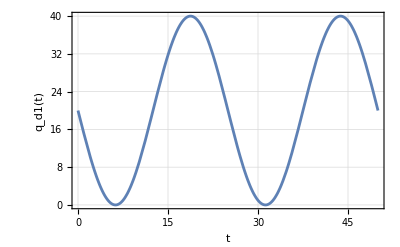

```mathematica
Plot[Subscript[q, d1][t],{t,0,Tman},PlotRange-> All,FrameLabel-> {"t","q_d1(t)"},Frame->True,GridLines-> Automatic]
```

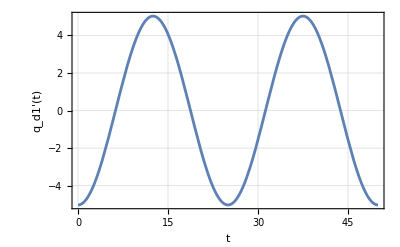

```mathematica
Plot[Subscript[q, d1]'[t],{t,0,Tman},PlotRange-> All,FrameLabel-> {"t","q_d1'(t)"},Frame->True,GridLines-> Automatic]
```

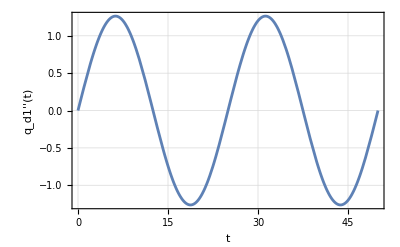

```mathematica
Plot[Subscript[q, d1]''[t],{t,0,Tman},PlotRange-> All,FrameLabel-> {"t","q_d1''(t)"},Frame->True,GridLines-> Automatic]
```

#### q_2 desired

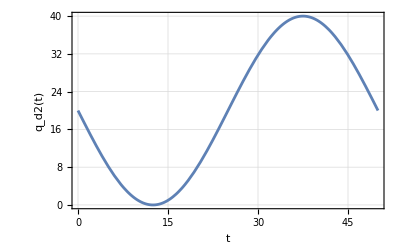

```mathematica
Plot[Subscript[q, d2][t],{t,0,Tman},PlotRange-> All,FrameLabel-> {"t","q_d2(t)"},Frame->True,GridLines-> Automatic]
```

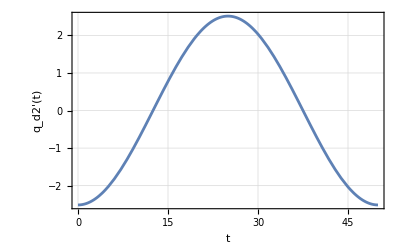

```mathematica
Plot[Subscript[q, d2]'[t],{t,0,Tman},PlotRange-> All,FrameLabel-> {"t","q_d2'(t)"},Frame->True,GridLines-> Automatic]
```

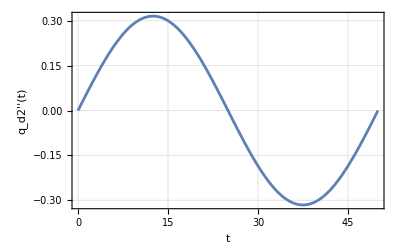

```mathematica
Plot[Subscript[q, d2]''[t],{t,0,Tman},PlotRange-> All,FrameLabel-> {"t","q_d2''(t)"},Frame->True,GridLines-> Automatic]
```

#### q_3 desired

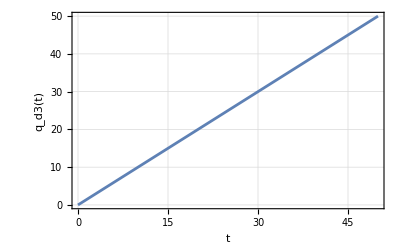

```mathematica
Plot[Subscript[q, d3][t],{t,0,Tman},PlotRange-> All,FrameLabel-> {"t","q_d3(t)"},Frame->True,GridLines-> Automatic]
```

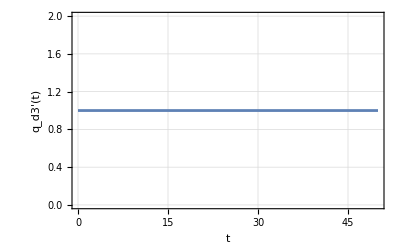

```mathematica
Plot[Subscript[q, d3]'[t],{t,0,Tman},PlotRange-> All,FrameLabel-> {"t","q_d3'(t)"},Frame->True,GridLines-> Automatic]
```

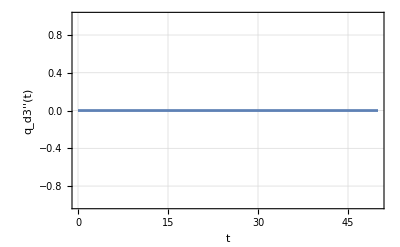

```mathematica
Plot[Subscript[q, d3]''[t],{t,0,Tman},PlotRange-> All,FrameLabel-> {"t","q_d3''(t)"},Frame->True,GridLines-> Automatic]
```

#### q_4 desired

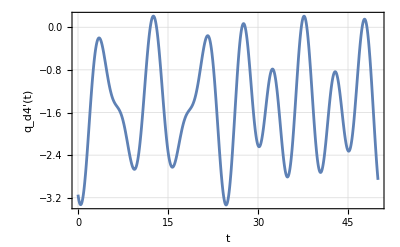

```mathematica
Plot[Subscript[q, d4]'[t],{t,0,Tman},PlotRange-> All,FrameLabel-> {"t","q_d4'(t)"},Frame->True,GridLines-> Automatic]
```

q_d4[t] After Integration

```mathematica
Subscript[q, d4][t_]=Integrate[Subscript[q, d4]'[t],{t,0,t}]
```

-0.8512-1.46667 t-1.78849 Cos[(2 π t)/25] Sin[t]+0.106965 Sin[t] Sin[(π t)/25]+Cos[t] (0.8512 Cos[(π t)/25]+0.449496 Sin[(2 π t)/25])

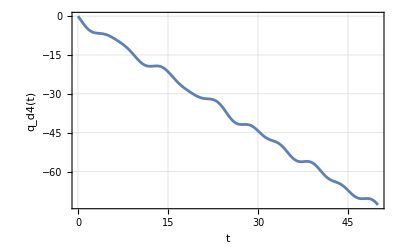

```mathematica
Plot[Subscript[q, d4][t],{t,0,Tman},PlotRange-> All,FrameLabel-> {"t","q_d4(t)"},Frame->True,GridLines-> Automatic]
```

q_d4''[t] After Integration

```mathematica
Subscript[q, d4]''[t]
```

0.0268832 Cos[t] Cos[(π t)/25]+1.90146 Cos[(2 π t)/25] Sin[t]-2 Sin[t] (0.112971 Cos[(2 π t)/25]-0.106965 Sin[(π t)/25])-0.108654 Sin[t] Sin[(π t)/25]+Cos[t] (-0.0134416 Cos[(π t)/25]-0.0283926 Sin[(2 π t)/25])-Cos[t] (0.8512 Cos[(π t)/25]+0.449496 Sin[(2 π t)/25])+0.898991 Cos[t] Sin[(2 π t)/25]

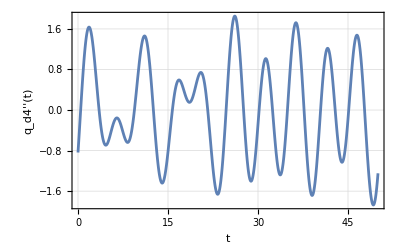

```mathematica
Plot[Subscript[q, d4]''[t],{t,0,Tman},PlotRange-> All,FrameLabel-> {"t","q_d4''(t)"},Frame->True,GridLines-> Automatic]
```

#### q_5 desired

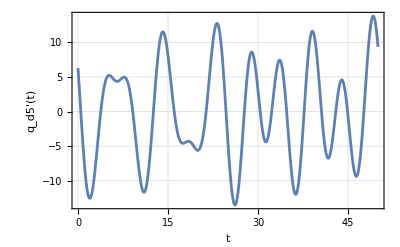

```mathematica
Plot[Subscript[q, d5]'[t],{t,0,Tman},PlotRange-> All,FrameLabel-> {"t","q_d5'(t)"},Frame->True,GridLines-> Automatic]
```

q_d5[t] After Integration

```mathematica
Subscript[q, d5][t_]=Integrate[Subscript[q, d5]'[t],{t,0,t}]
```

-13.4137+6.384 Cos[(π t)/25] Sin[t]+Cos[t] (13.4137 Cos[(2 π t)/25]-0.802237 Sin[(π t)/25])+3.37122 Sin[t] Sin[(2 π t)/25]

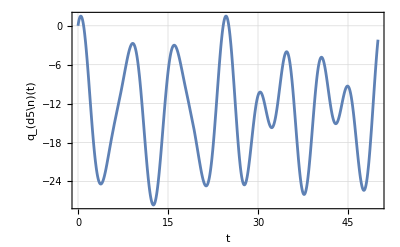

```mathematica
Plot[Subscript[q, d5][t],{t,0,Tman},PlotRange-> All,FrameLabel-> {"t","q_(d5\n)(t)"},Frame->True,GridLines-> Automatic]
```

q_d5''[t] After Integration

```mathematica
Subscript[q, d5]''[t]
```

1.69456 Cos[t] Cos[(2 π t)/25]-6.48481 Cos[(π t)/25] Sin[t]-Cos[t] (13.4137 Cos[(2 π t)/25]-0.802237 Sin[(π t)/25])+Cos[t] (-0.847279 Cos[(2 π t)/25]+0.0126684 Sin[(π t)/25])-1.60447 Cos[t] Sin[(π t)/25]-2 Sin[t] (-0.100812 Cos[(π t)/25]-3.37122 Sin[(2 π t)/25])-3.58416 Sin[t] Sin[(2 π t)/25]

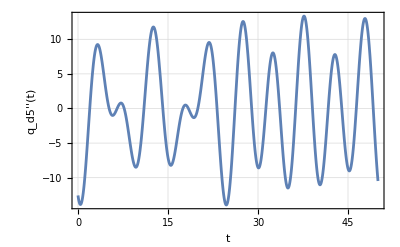

```mathematica
Plot[Subscript[q, d5]''[t],{t,0,Tman},PlotRange-> All,FrameLabel-> {"t","q_d5''(t)"},Frame->True,GridLines-> Automatic]
```

#### q_6 desired

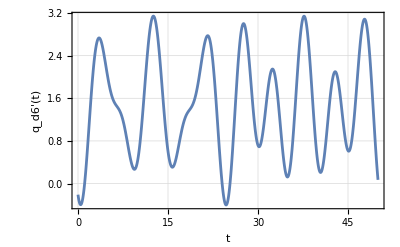

```mathematica
Plot[Subscript[q, d6]'[t],{t,0,Tman},PlotRange-> All,FrameLabel-> {"t","q_d6'(t)"},Frame->True,GridLines-> Automatic]
```

q_6[t] After Integration

```mathematica
Subscript[q, d6][t_]=Integrate[Subscript[q, d6]'[t],{t,0,t}]
```

-0.8512+1.46667 t-1.78849 Cos[(2 π t)/25] Sin[t]+0.106965 Sin[t] Sin[(π t)/25]+Cos[t] (0.8512 Cos[(π t)/25]+0.449496 Sin[(2 π t)/25])

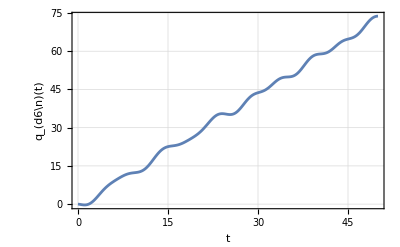

```mathematica
Plot[Subscript[q, d6][t],{t,0,Tman},PlotRange-> All,FrameLabel-> {"t","q_(d6\n)(t)"},Frame->True,GridLines-> Automatic]
```

q_d6''[t] After Integration

```mathematica
Subscript[q, d6]''[t]
```

0.0268832 Cos[t] Cos[(π t)/25]+1.90146 Cos[(2 π t)/25] Sin[t]-2 Sin[t] (0.112971 Cos[(2 π t)/25]-0.106965 Sin[(π t)/25])-0.108654 Sin[t] Sin[(π t)/25]+Cos[t] (-0.0134416 Cos[(π t)/25]-0.0283926 Sin[(2 π t)/25])-Cos[t] (0.8512 Cos[(π t)/25]+0.449496 Sin[(2 π t)/25])+0.898991 Cos[t] Sin[(2 π t)/25]

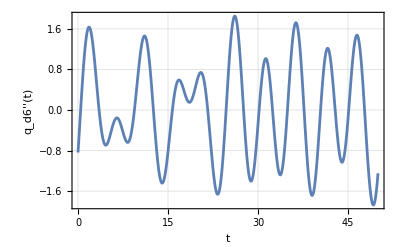

```mathematica
Plot[Subscript[q, d6]''[t],{t,0,Tman},PlotRange-> All,FrameLabel-> {"t","q_d6''(t)"},Frame->True,GridLines-> Automatic]
```

#### q_7 desired

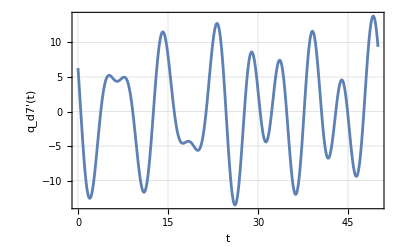

```mathematica
Plot[Subscript[q, d7]'[t],{t,0,Tman},PlotRange-> All,FrameLabel-> {"t","q_d7'(t)"},Frame->True,GridLines-> Automatic]
```

q_d7[t] After Integration

```mathematica
Subscript[q, d7][t_]=Integrate[Subscript[q, d7]'[t],{t,0,t}]
```

-13.4137+6.384 Cos[(π t)/25] Sin[t]+Cos[t] (13.4137 Cos[(2 π t)/25]-0.802237 Sin[(π t)/25])+3.37122 Sin[t] Sin[(2 π t)/25]

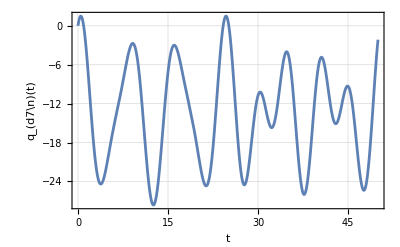

```mathematica
Plot[Subscript[q, d7][t],{t,0,Tman},PlotRange-> All,FrameLabel-> {"t","q_(d7\n)(t)"},Frame->True,GridLines-> Automatic]
```

q_7''[t] After Integration

```mathematica
Subscript[q, d7]''[t]
```

1.69456 Cos[t] Cos[(2 π t)/25]-6.48481 Cos[(π t)/25] Sin[t]-Cos[t] (13.4137 Cos[(2 π t)/25]-0.802237 Sin[(π t)/25])+Cos[t] (-0.847279 Cos[(2 π t)/25]+0.0126684 Sin[(π t)/25])-1.60447 Cos[t] Sin[(π t)/25]-2 Sin[t] (-0.100812 Cos[(π t)/25]-3.37122 Sin[(2 π t)/25])-3.58416 Sin[t] Sin[(2 π t)/25]

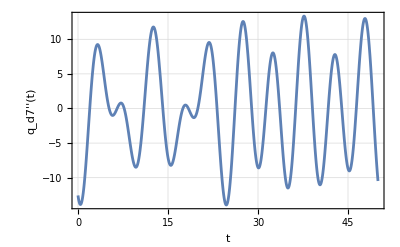

```mathematica
Plot[Subscript[q, d7]''[t],{t,0,Tman},PlotRange-> All,FrameLabel-> {"t","q_d7''(t)"},Frame->True,GridLines-> Automatic]
```

#### q_8 desired

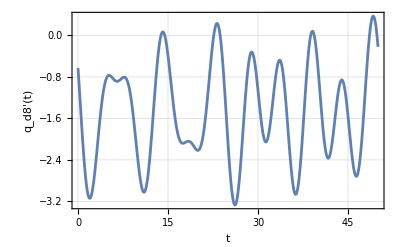

```mathematica
Plot[Subscript[q, d8]'[t],{t,0,Tman},PlotRange-> All,FrameLabel-> {"t","q_d8'(t)"},Frame->True,GridLines-> Automatic]
```

q_8[t] After Integration

```mathematica
Subscript[q, d8][t_]=Integrate[Subscript[q, d8]'[t],{t,0,t}]
```

-1.78849-1.46667 t+0.8512 Cos[(π t)/25] Sin[t]+Cos[t] (1.78849 Cos[(2 π t)/25]-0.106965 Sin[(π t)/25])+0.449496 Sin[t] Sin[(2 π t)/25]

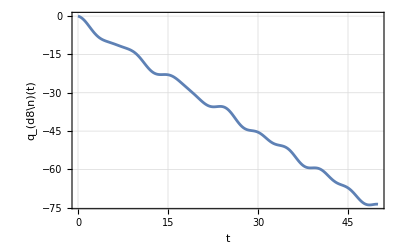

```mathematica
Plot[Subscript[q, d8][t],{t,0,Tman},PlotRange-> All,FrameLabel-> {"t","q_(d8\n)(t)"},Frame->True,GridLines-> Automatic]
```

q_8''[t] After Integration

```mathematica
Subscript[q, d8]''[t]
```

0.225941 Cos[t] Cos[(2 π t)/25]-0.864641 Cos[(π t)/25] Sin[t]-Cos[t] (1.78849 Cos[(2 π t)/25]-0.106965 Sin[(π t)/25])+Cos[t] (-0.112971 Cos[(2 π t)/25]+0.00168912 Sin[(π t)/25])-0.21393 Cos[t] Sin[(π t)/25]-2 Sin[t] (-0.0134416 Cos[(π t)/25]-0.449496 Sin[(2 π t)/25])-0.477888 Sin[t] Sin[(2 π t)/25]

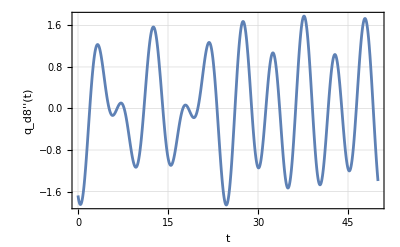

```mathematica
Plot[Subscript[q, d8]''[t],{t,0,Tman},PlotRange-> All,FrameLabel-> {"t","q_d8''(t)"},Frame->True,GridLines-> Automatic]
```

#### q_9 desired

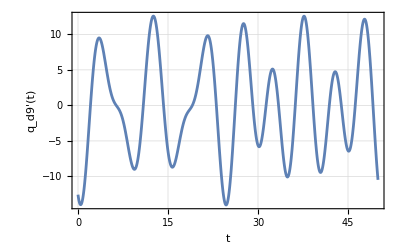

```mathematica
Plot[Subscript[q, d9]'[t],{t,0,Tman},PlotRange-> All,FrameLabel-> {"t","q_d9'(t)"},Frame->True,GridLines-> Automatic]
```

q_d9[t] After Integration

```mathematica
Subscript[q, d9][t_]=Integrate[Subscript[q, d9]'[t],{t,0,t}]
```

-6.384-13.4137 Cos[(2 π t)/25] Sin[t]+0.802237 Sin[t] Sin[(π t)/25]+Cos[t] (6.384 Cos[(π t)/25]+3.37122 Sin[(2 π t)/25])

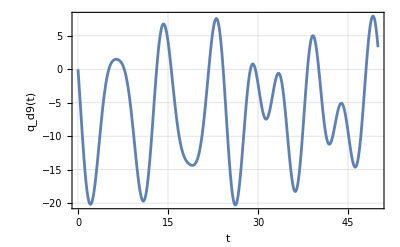

```mathematica
Plot[Subscript[q, d9][t],{t,0,Tman},PlotRange-> All,FrameLabel-> {"t","q_d9(t)"},Frame->True,GridLines-> Automatic]
```

q_d9''[t] After Integration

```mathematica
Subscript[q, d9]''[t]
```

0.201624 Cos[t] Cos[(π t)/25]+14.2609 Cos[(2 π t)/25] Sin[t]-2 Sin[t] (0.847279 Cos[(2 π t)/25]-0.802237 Sin[(π t)/25])-0.814905 Sin[t] Sin[(π t)/25]+Cos[t] (-0.100812 Cos[(π t)/25]-0.212945 Sin[(2 π t)/25])+6.74244 Cos[t] Sin[(2 π t)/25]-Cos[t] (6.384 Cos[(π t)/25]+3.37122 Sin[(2 π t)/25])

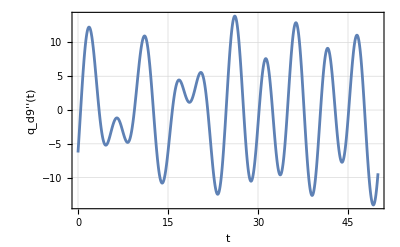

```mathematica
Plot[Subscript[q, d9]''[t],{t,0,Tman},PlotRange-> All,FrameLabel-> {"t","q_d9''(t)"},Frame->True,GridLines-> Automatic]
```

#### q_10 desired

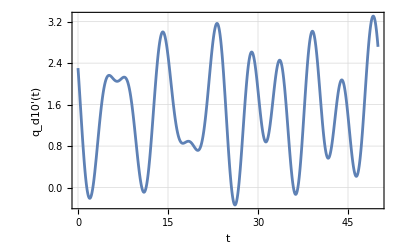

```mathematica
Plot[Subscript[q, d10]'[t],{t,0,Tman},PlotRange-> All,FrameLabel-> {"t","q_d10'(t)"},Frame->True,GridLines-> Automatic]
```

q_d10[t] After Integration

```mathematica
Subscript[q, d10][t_]=Integrate[Subscript[q, d10]'[t],{t,0,t}]
```

-1.78849+1.46667 t+0.8512 Cos[(π t)/25] Sin[t]+Cos[t] (1.78849 Cos[(2 π t)/25]-0.106965 Sin[(π t)/25])+0.449496 Sin[t] Sin[(2 π t)/25]

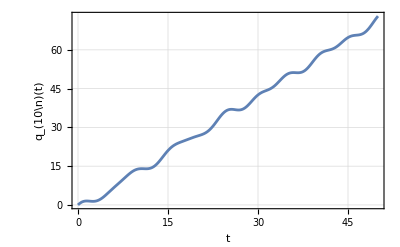

```mathematica
Plot[Subscript[q, d10][t],{t,0,Tman},PlotRange-> All,FrameLabel-> {"t","q_(10\n)(t)"},Frame->True,GridLines-> Automatic]
```

q_d10''[t] After Integration

```mathematica
Subscript[q, d10]''[t]
```

0.225941 Cos[t] Cos[(2 π t)/25]-0.864641 Cos[(π t)/25] Sin[t]-Cos[t] (1.78849 Cos[(2 π t)/25]-0.106965 Sin[(π t)/25])+Cos[t] (-0.112971 Cos[(2 π t)/25]+0.00168912 Sin[(π t)/25])-0.21393 Cos[t] Sin[(π t)/25]-2 Sin[t] (-0.0134416 Cos[(π t)/25]-0.449496 Sin[(2 π t)/25])-0.477888 Sin[t] Sin[(2 π t)/25]

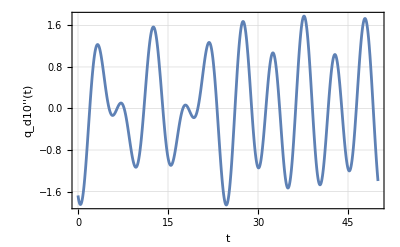

```mathematica
Plot[Subscript[q, d10]''[t],{t,0,Tman},PlotRange-> All,FrameLabel-> {"t","q_d10''(t)"},Frame->True,GridLines-> Automatic]
```

#### q_11 desired

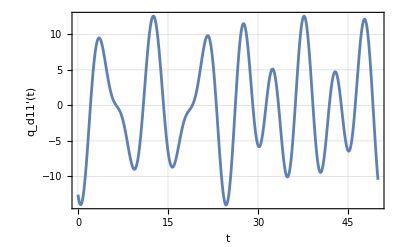

```mathematica
Plot[Subscript[q, d11]'[t],{t,0,Tman},PlotRange-> All,FrameLabel-> {"t","q_d11'(t)"},Frame->True,GridLines-> Automatic]
```

q_d11[t] After Integration

```mathematica
Subscript[q, d11][t_]=Integrate[Subscript[q, d11]'[t],{t,0,t}]
```

-6.384-13.4137 Cos[(2 π t)/25] Sin[t]+0.802237 Sin[t] Sin[(π t)/25]+Cos[t] (6.384 Cos[(π t)/25]+3.37122 Sin[(2 π t)/25])

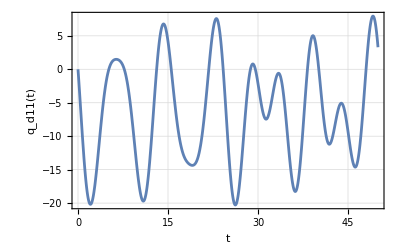

```mathematica
Plot[Subscript[q, d11][t],{t,0,Tman},PlotRange-> All,FrameLabel-> {"t","q_d11(t)"},Frame->True,GridLines-> Automatic]
```

q_d11''[t] After Integration

```mathematica
Subscript[q, d11]''[t]
```

0.201624 Cos[t] Cos[(π t)/25]+14.2609 Cos[(2 π t)/25] Sin[t]-2 Sin[t] (0.847279 Cos[(2 π t)/25]-0.802237 Sin[(π t)/25])-0.814905 Sin[t] Sin[(π t)/25]+Cos[t] (-0.100812 Cos[(π t)/25]-0.212945 Sin[(2 π t)/25])+6.74244 Cos[t] Sin[(2 π t)/25]-Cos[t] (6.384 Cos[(π t)/25]+3.37122 Sin[(2 π t)/25])

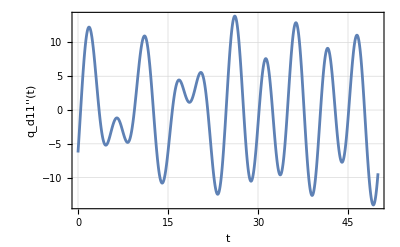

```mathematica
Plot[Subscript[q, d11]''[t],{t,0,Tman},PlotRange-> All,FrameLabel-> {"t","q_d11''(t)"},Frame->True,GridLines-> Automatic]
```

#### Path Planned Kinematics Animation

Here we create a simple path plan to get form the rest position to the desired position.

```mathematica
Subscript[q, 1][t_]=Subscript[q, d1][t];
Subscript[q, 2][t_]=Subscript[q, d2][t];
Subscript[q, 3][t_]=Subscript[q, d3][t];
Subscript[q, 4][t_]=Subscript[q, d4][t];
Subscript[q, 5][t_]=Subscript[q, d5][t];
Subscript[q, 6][t_]=Subscript[q, d6][t];
Subscript[q, 7][t_]=Subscript[q, d7][t];
Subscript[q, 8][t_]=Subscript[q, d8][t];
Subscript[q, 9][t_]=Subscript[q, d9][t];
Subscript[q, 10][t_]=Subscript[q, d10][t];
Subscript[q, 11][t_]=Subscript[q, d11][t];
```

Create composite graphic out of parts that have been rotated and translated

```mathematica
pathPlot=ParametricPlot3D[{Subscript[q, d1][t],Subscript[q, d2][t],Subscript[q, z][t]},{t,0,Tman},ViewPoint->{1,-1,1},ViewVertical->{0,0,1},ViewCenter->{1/2,1/2,1/2},Boxed->True,Axes->True,PlotRange->{{-6,50},{-6,50},{-6,50}},AspectRatio->1,AxesLabel->{"q_d1","q_d2","q_z"}]
```

-Graphics3D-

```mathematica
ParametricPlot3D[{Subscript[q, d1][t],Subscript[q, d2][t],Subscript[q, z][t]},{t,0,Tman},ViewPoint->{1,-1,1},ViewVertical->{0,0,1},ViewCenter->{1/2,1/2,1/2},Boxed->True,Axes->True,PlotRange->{{-6,50},{-6,50},{-6,50}},AspectRatio->1,AxesLabel->{"q_d1","q_d2","q_d3"}]
```

-Graphics3D-

```mathematica
robotGraphicPathKinAnim={
(*Base graphic*)
Translate[GeometricTransformation[baseGraphic,Transpose[rotA]],{xA,yA,zA}],

(*Wheel graphic*)
Translate[GeometricTransformation[comwheelGraphic1,Transpose[rotB]],{xB,yB,zB}],
Translate[GeometricTransformation[barrelGraphic1,Transpose[rotC]],{xC,yC,zC}],
Translate[GeometricTransformation[comwheelGraphic2,Transpose[rotD]],{xD,yD,zD}],
Translate[GeometricTransformation[comwheelGraphic3,Transpose[rotF]],{xF,yF,zF}],
Translate[GeometricTransformation[comwheelGraphic4,Transpose[rotH]],{xH,yH,zH}]
};
```

```mathematica
robotGraphicPathKinAnimT[t_]=robotGraphicPathKinAnim;
```

Loop over time

```mathematica
(*{-0.15scale,scale},{-0.15scale,0.15scale},{-scale,scale}*)
```

```mathematica
Animate[Show[pathPlot,Graphics3D[robotGraphicPathKinAnimT[t],ViewPoint->{1,1,1},ViewVertical->{0,0,1},ViewCenter->{1/2,1/2,1/2},Boxed->True,Axes->True,PlotRange->{{-6,50},{-6,50},{-6,50}},AspectRatio->1,AxesLabel->{"X","Y","Z"}]],{t,0,Tman,delT},AnimationRunning->False]
```

### Solve for PID

#### Clearing variables

First clear all the variables of the kinematics.  Sometimes this may cause an error if they have not been assigned numbers yet. Ignore the error and proceed.

```mathematica
p4[t_]=.;
p6[t_]=.;
p8[t_]=.;
p10[t_]=.;
q1[t_]=.;
q2[t_]=.;
q3[t_]=.;
q4[t_]=.;
q5[t_]=.;
q6[t_]=.;
q7[t_]=.;
q8[t_]=.;
q9[t_]=.;
q10[t_]=.;
q11[t_]=.;
Subscript[q, 1][t_]=.;
Subscript[q, 2][t_]=.;
Subscript[q, 3][t_]=.;
Subscript[q, 4][t_]=.;
Subscript[q, 5][t_]=.;
Subscript[q, 6][t_]=.;
Subscript[q, 7][t_]=.;
Subscript[q, 8][t_]=.;
Subscript[q, 9][t_]=.;
Subscript[q, 10][t_]=.;
Subscript[q, 11][t_]=.;
Subscript[q, 1]'[t_]=.;
Subscript[q, 2]'[t_]=.;
Subscript[q, 3]'[t_]=.;
Subscript[q, 4]'[t_]=.;
Subscript[q, 5]'[t_]=.;
Subscript[q, 6]'[t_]=.;
Subscript[q, 7]'[t_]=.;
Subscript[q, 8]'[t_]=.;
Subscript[q, 9]'[t_]=.;
Subscript[q, 10]'[t_]=.;
Subscript[q, 11]'[t_]=.;
Subscript[q, 1]''[t_]=.;
Subscript[q, 2]''[t_]=.;
Subscript[q, 3]''[t_]=.;
Subscript[q, 4]''[t_]=.;
Subscript[q, 5]''[t_]=.;
Subscript[q, 6]''[t_]=.;
Subscript[q, 7]''[t_]=.;
Subscript[q, 8]''[t_]=.;
Subscript[q, 9]''[t_]=.;
Subscript[q, 10]''[t_]=.;
Subscript[q, 11]''[t_]=.;
Subscript[Q, 1][t_]=.;
Subscript[Q, 2][t_]=.;
Subscript[Q, 3][t_]=.;
Subscript[Q, 4][t_]=.;
Subscript[Q, 5][t_]=.;
Subscript[Q, 6][t_]=.;
Subscript[Q, 7][t_]=.;
Subscript[Q, 8][t_]=.;
Subscript[Q, 9][t_]=.;
Subscript[Q, 10][t_]=.;
Subscript[Q, 11][t_]=.;
Subscript[ω, 1][t_]=.;
Subscript[ω, 2][t_]=.;
Subscript[ω, 3][t_]=.;
Subscript[ω, 4][t_]=.;
ω=.;
A=.;
B=.;
Cc=.;
r=.;
R=.;
t=.;
Ω=.;
A1=.;
A2=.;
A3=.;
A4=.;
A6=.;
A8=.;
A10=.;
B4=.;
B6=.;
B8=.;
B10=.;
b4=.;
b6=.;
b8=.;
b10=.;
Subscript[T, mot][1]=.;
Subscript[T, mot][2]=.;
Subscript[T, mot][3]=.;
Subscript[T, mot][4]=.;
Tmot1[t_]=.;
Tmot2[t_]=.;
Tmot3[t_]=.;
Tmot4[t_]=.;
Tmot1=.;
Tmot2=.;
Tmot3=.;
Tmot4=.;
q=.;
Q=.;
p4=.;
p6=.;
p8=.;
p10=.;
```

Unset::norep: Assignment on p4 for p4[t_] not found.

Unset::norep: Assignment on p6 for p6[t_] not found.

Unset::norep: Assignment on p8 for p8[t_] not found.

Unset::norep: Assignment on p10 for p10[t_] not found.

Unset::norep: Assignment on q1 for q1[t_] not found.

Unset::norep: Assignment on q2 for q2[t_] not found.

Unset::norep: Assignment on q3 for q3[t_] not found.

Unset::norep: Assignment on q4 for q4[t_] not found.

Unset::norep: Assignment on q5 for q5[t_] not found.

Unset::norep: Assignment on q6 for q6[t_] not found.

Unset::norep: Assignment on q7 for q7[t_] not found.

Unset::norep: Assignment on q8 for q8[t_] not found.

Unset::norep: Assignment on q9 for q9[t_] not found.

Unset::norep: Assignment on q10 for q10[t_] not found.

Unset::norep: Assignment on q11 for q11[t_] not found.

Unset::norep: Assignment on Derivative for q_1'[t_] not found.

Unset::norep: Assignment on Derivative for q_2'[t_] not found.

Unset::norep: Assignment on Derivative for q_3'[t_] not found.

Unset::norep: Assignment on Derivative for q_4'[t_] not found.

Unset::norep: Assignment on Derivative for q_5'[t_] not found.

Unset::norep: Assignment on Derivative for q_6'[t_] not found.

Unset::norep: Assignment on Derivative for q_7'[t_] not found.

Unset::norep: Assignment on Derivative for q_8'[t_] not found.

Unset::norep: Assignment on Derivative for q_9'[t_] not found.

Unset::norep: Assignment on Derivative for q_10'[t_] not found.

Unset::norep: Assignment on Derivative for q_11'[t_] not found.

Unset::norep: Assignment on Derivative for q_1''[t_] not found.

Unset::norep: Assignment on Derivative for q_2''[t_] not found.

Unset::norep: Assignment on Derivative for q_3''[t_] not found.

Unset::norep: Assignment on Derivative for q_4''[t_] not found.

Unset::norep: Assignment on Derivative for q_5''[t_] not found.

Unset::norep: Assignment on Derivative for q_6''[t_] not found.

Unset::norep: Assignment on Derivative for q_7''[t_] not found.

Unset::norep: Assignment on Derivative for q_8''[t_] not found.

Unset::norep: Assignment on Derivative for q_9''[t_] not found.

Unset::norep: Assignment on Derivative for q_10''[t_] not found.

Unset::norep: Assignment on Derivative for q_11''[t_] not found.

Unset::norep: Assignment on Subscript for Q_1[t_] not found.

Unset::norep: Assignment on Subscript for Q_2[t_] not found.

Unset::norep: Assignment on Subscript for Q_3[t_] not found.

Unset::norep: Assignment on Subscript for Q_4[t_] not found.

Unset::norep: Assignment on Subscript for Q_5[t_] not found.

Unset::norep: Assignment on Subscript for Q_6[t_] not found.

Unset::norep: Assignment on Subscript for Q_7[t_] not found.

Unset::norep: Assignment on Subscript for Q_8[t_] not found.

Unset::norep: Assignment on Subscript for Q_9[t_] not found.

Unset::norep: Assignment on Subscript for Q_10[t_] not found.

Unset::norep: Assignment on Subscript for Q_11[t_] not found.

Unset::norep: Assignment on Subscript for (π/25)_1[t_] not found.

Unset::norep: Assignment on Subscript for (π/25)_2[t_] not found.

Unset::norep: Assignment on Subscript for (π/25)_3[t_] not found.

Unset::norep: Assignment on Subscript for (π/25)_4[t_] not found.

Unset::norep: Assignment on Subscript for ((0.+0.113144 q_1'[t]^2+0.113144 q_2'[t]^2+2.23361 q_3'[t]^2+0.0106086 Cos[2 q_4[t]] q_3'[t]^2+0.0102215 Cos[2 q_6[t]] («1»'[t])^2+0.000027723 Cos[2 q_8[t]] q_3'[t]^2+0.000027723 Cos[2 q_10[t]] q_3'[t]^2+0.0699246 q_4'[t]^2-0.000110892 Sin[q_4[t]] q_3'[t] q_5'[t]+«13»)_mot)[1] not found.

Unset::norep: Assignment on Subscript for ((0.+0.113144 q_1'[t]^2+0.113144 q_2'[t]^2+2.23361 q_3'[t]^2+0.0106086 Cos[2 q_4[t]] q_3'[t]^2+0.0102215 Cos[2 q_6[t]] («1»'[t])^2+0.000027723 Cos[2 q_8[t]] q_3'[t]^2+0.000027723 Cos[2 q_10[t]] q_3'[t]^2+0.0699246 q_4'[t]^2-0.000110892 Sin[q_4[t]] q_3'[t] q_5'[t]+«13»)_mot)[2] not found.

Unset::norep: Assignment on Subscript for ((0.+0.113144 q_1'[t]^2+0.113144 q_2'[t]^2+2.23361 q_3'[t]^2+0.0106086 Cos[2 q_4[t]] q_3'[t]^2+0.0102215 Cos[2 q_6[t]] («1»'[t])^2+0.000027723 Cos[2 q_8[t]] q_3'[t]^2+0.000027723 Cos[2 q_10[t]] q_3'[t]^2+0.0699246 q_4'[t]^2-0.000110892 Sin[q_4[t]] q_3'[t] q_5'[t]+«13»)_mot)[3] not found.

Unset::norep: Assignment on Subscript for ((0.+0.113144 q_1'[t]^2+0.113144 q_2'[t]^2+2.23361 q_3'[t]^2+0.0106086 Cos[2 q_4[t]] q_3'[t]^2+0.0102215 Cos[2 q_6[t]] («1»'[t])^2+0.000027723 Cos[2 q_8[t]] q_3'[t]^2+0.000027723 Cos[2 q_10[t]] q_3'[t]^2+0.0699246 q_4'[t]^2-0.000110892 Sin[q_4[t]] q_3'[t] q_5'[t]+«13»)_mot)[4] not found.

Unset::norep: Assignment on Tmot1 for Tmot1[t_] not found.

Unset::norep: Assignment on Tmot2 for Tmot2[t_] not found.

Unset::norep: Assignment on Tmot3 for Tmot3[t_] not found.

Unset::norep: Assignment on Tmot4 for Tmot4[t_] not found.

#### Gains

```mathematica
Subscript[K, prop][1]=1426.79;Subscript[K, Int][1]=17378.6;Subscript[K, deriv][1]=90.8426;
```

```mathematica
Subscript[K, prop][2]=1423.97;Subscript[K, Int][2]=17344.3;Subscript[K, deriv][2]=90.663;
```

```mathematica
Subscript[K, prop][3]=1498.26;Subscript[K, Int][3]=18249.1;Subscript[K, deriv][3]=95.3929;
```

```mathematica
Subscript[K, prop][4]=1498.26;Subscript[K, Int][4]=18249.1;Subscript[K, deriv][4]=95.3929;
```

#### Assigning and replacing variables

```mathematica
(*eom1n=eom1//.{Subscript[q, 4]'[t]-> q4p,Subscript[q, 6]'[t]-> q6p,Subscript[q, 8]'[t]-> q8p,Subscript[q, 10]'[t]-> q10p,p4'[t]->p4p,p6'[t]->p6p,p8'[t]->p8p,p10'[t]->p10p,Subscript[q, 4]''[t]-> q4dp,Subscript[q, 6]''[t]-> q6dp,Subscript[q, 8]''[t]-> q8dp,Subscript[q, 10]''[t]-> q10dp,Tmot[1]-> Tmot1[t],Tmot[2]-> Tmot2[t],Tmot[3]->Tmot3[t],Tmot[4]->Tmot4[t]};*)
```

```mathematica
(*eom2n=eom2//.{Subscript[q, 4]'[t]-> q4p,Subscript[q, 6]'[t]-> q6p,Subscript[q, 8]'[t]-> q8p,Subscript[q, 10]'[t]-> q10p,p4'[t]->p4p,p6'[t]->p6p,p8'[t]->p8p,p10'[t]->p10p,Subscript[q, 4]''[t]-> q4dp,Subscript[q, 6]''[t]-> q6dp,Subscript[q, 8]''[t]-> q8dp,Subscript[q, 10]''[t]-> q10dp,Tmot[1]-> Tmot1[t],Tmot[2]-> Tmot2[t],Tmot[3]->Tmot3[t],Tmot[4]->Tmot4[t]};*)
```

```mathematica
(*eom3n=eom3//.{Subscript[q, 4]'[t]-> q4p,Subscript[q, 6]'[t]-> q6p,Subscript[q, 8]'[t]-> q8p,Subscript[q, 10]'[t]-> q10p,p4'[t]->p4p,p6'[t]->p6p,p8'[t]->p8p,p10'[t]->p10p,Subscript[q, 4]''[t]-> q4dp,Subscript[q, 6]''[t]-> q6dp,Subscript[q, 8]''[t]-> q8dp,Subscript[q, 10]''[t]-> q10dp,Tmot[1]-> Tmot1[t],Tmot[2]-> Tmot2[t],Tmot[3]->Tmot3[t],Tmot[4]->Tmot4[t]};*)
```

```mathematica
(*eom4n=eom4//.{Subscript[q, 4]'[t]-> q4p,Subscript[q, 6]'[t]-> q6p,Subscript[q, 8]'[t]-> q8p,Subscript[q, 10]'[t]-> q10p,p4'[t]->p4p,p6'[t]->p6p,p8'[t]->p8p,p10'[t]->p10p,Subscript[q, 4]''[t]-> q4dp,Subscript[q, 6]''[t]-> q6dp,Subscript[q, 8]''[t]-> q8dp,Subscript[q, 10]''[t]-> q10dp,Tmot[1]-> Tmot1[t],Tmot[2]-> Tmot2[t],Tmot[3]->Tmot3[t],Tmot[4]->Tmot4[t]};*)
```

```mathematica
(*eom5n=eom5//.{Subscript[q, 4]'[t]-> q4p,Subscript[q, 6]'[t]-> q6p,Subscript[q, 8]'[t]-> q8p,Subscript[q, 10]'[t]-> q10p,p4'[t]->p4p,p6'[t]->p6p,p8'[t]->p8p,p10'[t]->p10p,Subscript[q, 4]''[t]-> q4dp,Subscript[q, 6]''[t]-> q6dp,Subscript[q, 8]''[t]-> q8dp,Subscript[q, 10]''[t]-> q10dp,Tmot[1]-> Tmot1[t],Tmot[2]-> Tmot2[t],Tmot[3]->Tmot3[t],Tmot[4]->Tmot4[t]};*)
```

```mathematica
(*eom6n=eom6//.{Subscript[q, 4]'[t]-> q4p,Subscript[q, 6]'[t]-> q6p,Subscript[q, 8]'[t]-> q8p,Subscript[q, 10]'[t]-> q10p,p4'[t]->p4p,p6'[t]->p6p,p8'[t]->p8p,p10'[t]->p10p,Subscript[q, 4]''[t]-> q4dp,Subscript[q, 6]''[t]-> q6dp,Subscript[q, 8]''[t]-> q8dp,Subscript[q, 10]''[t]-> q10dp,Tmot[1]-> Tmot1[t],Tmot[2]-> Tmot2[t],Tmot[3]->Tmot3[t],Tmot[4]->Tmot4[t]};*)
```

```mathematica
(*eom7n=eom7//.{Subscript[q, 4]'[t]-> q4p,Subscript[q, 6]'[t]-> q6p,Subscript[q, 8]'[t]-> q8p,Subscript[q, 10]'[t]-> q10p,p4'[t]->p4p,p6'[t]->p6p,p8'[t]->p8p,p10'[t]->p10p,Subscript[q, 4]''[t]-> q4dp,Subscript[q, 6]''[t]-> q6dp,Subscript[q, 8]''[t]-> q8dp,Subscript[q, 10]''[t]-> q10dp,Tmot[1]-> Tmot1[t],Tmot[2]-> Tmot2[t],Tmot[3]->Tmot3[t],Tmot[4]->Tmot4[t]};*)
```

```mathematica
(*eom8n=eom8//.{Subscript[q, 4]'[t]-> q4p,Subscript[q, 6]'[t]-> q6p,Subscript[q, 8]'[t]-> q8p,Subscript[q, 10]'[t]-> q10p,p4'[t]->p4p,p6'[t]->p6p,p8'[t]->p8p,p10'[t]->p10p,Subscript[q, 4]''[t]-> q4dp,Subscript[q, 6]''[t]-> q6dp,Subscript[q, 8]''[t]-> q8dp,Subscript[q, 10]''[t]-> q10dp,Tmot[1]-> Tmot1[t],Tmot[2]-> Tmot2[t],Tmot[3]->Tmot3[t],Tmot[4]->Tmot4[t]};*)
```

```mathematica
(*eom9n=eom9//.{Subscript[q, 4]'[t]-> q4p,Subscript[q, 6]'[t]-> q6p,Subscript[q, 8]'[t]-> q8p,Subscript[q, 10]'[t]-> q10p,p4'[t]->p4p,p6'[t]->p6p,p8'[t]->p8p,p10'[t]->p10p,Subscript[q, 4]''[t]-> q4dp,Subscript[q, 6]''[t]-> q6dp,Subscript[q, 8]''[t]-> q8dp,Subscript[q, 10]''[t]-> q10dp,Tmot[1]-> Tmot1[t],Tmot[2]-> Tmot2[t],Tmot[3]->Tmot3[t],Tmot[4]->Tmot4[t]};*)
```

```mathematica
(*eom10n=eom10//.{Subscript[q, 4]'[t]-> q4p,Subscript[q, 6]'[t]-> q6p,Subscript[q, 8]'[t]-> q8p,Subscript[q, 10]'[t]-> q10p,p4'[t]->p4p,p6'[t]->p6p,p8'[t]->p8p,p10'[t]->p10p,Subscript[q, 4]''[t]-> q4dp,Subscript[q, 6]''[t]-> q6dp,Subscript[q, 8]''[t]-> q8dp,Subscript[q, 10]''[t]-> q10dp,Tmot[1]-> Tmot1[t],Tmot[2]-> Tmot2[t],Tmot[3]->Tmot3[t],Tmot[4]->Tmot4[t]};*)
```

```mathematica
(*eom11n=eom11//.{Subscript[q, 4]'[t]-> q4p,Subscript[q, 6]'[t]-> q6p,Subscript[q, 8]'[t]-> q8p,Subscript[q, 10]'[t]-> q10p,p4'[t]->p4p,p6'[t]->p6p,p8'[t]->p8p,p10'[t]->p10p,Subscript[q, 4]''[t]-> q4dp,Subscript[q, 6]''[t]-> q6dp,Subscript[q, 8]''[t]-> q8dp,Subscript[q, 10]''[t]-> q10dp,Tmot[1]-> Tmot1[t],Tmot[2]-> Tmot2[t],Tmot[3]->Tmot3[t],Tmot[4]->Tmot4[t]};*)
```

```mathematica
(*eom12n=eom12//.{Subscript[q, 4]'[t]-> q4p,Subscript[q, 6]'[t]-> q6p,Subscript[q, 8]'[t]-> q8p,Subscript[q, 10]'[t]-> q10p,p4'[t]->p4p,p6'[t]->p6p,p8'[t]->p8p,p10'[t]->p10p,Subscript[q, 4]''[t]-> q4dp,Subscript[q, 6]''[t]-> q6dp,Subscript[q, 8]''[t]-> q8dp,Subscript[q, 10]''[t]-> q10dp,Tmot[1]-> Tmot1[t],Tmot[2]-> Tmot2[t],Tmot[3]->Tmot3[t],Tmot[4]->Tmot4[t]};*)
```

```mathematica
(*eom13n=eom13//.{Subscript[q, 4]'[t]-> q4p,Subscript[q, 6]'[t]-> q6p,Subscript[q, 8]'[t]-> q8p,Subscript[q, 10]'[t]-> q10p,p4'[t]->p4p,p6'[t]->p6p,p8'[t]->p8p,p10'[t]->p10p,Subscript[q, 4]''[t]-> q4dp,Subscript[q, 6]''[t]-> q6dp,Subscript[q, 8]''[t]-> q8dp,Subscript[q, 10]''[t]-> q10dp,Tmot[1]-> Tmot1[t],Tmot[2]-> Tmot2[t],Tmot[3]->Tmot3[t],Tmot[4]->Tmot4[t]};*)
```

```mathematica
(*eom14n=eom14//.{Subscript[q, 4]'[t]-> q4p,Subscript[q, 6]'[t]-> q6p,Subscript[q, 8]'[t]-> q8p,Subscript[q, 10]'[t]-> q10p,p4'[t]->p4p,p6'[t]->p6p,p8'[t]->p8p,p10'[t]->p10p,Subscript[q, 4]''[t]-> q4dp,Subscript[q, 6]''[t]-> q6dp,Subscript[q, 8]''[t]-> q8dp,Subscript[q, 10]''[t]-> q10dp,Tmot[1]-> Tmot1[t],Tmot[2]-> Tmot2[t],Tmot[3]->Tmot3[t],Tmot[4]->Tmot4[t]};*)
```

```mathematica
(*eom15n=eom15//.{Subscript[q, 4]'[t]-> q4p,Subscript[q, 6]'[t]-> q6p,Subscript[q, 8]'[t]-> q8p,Subscript[q, 10]'[t]-> q10p,p4'[t]->p4p,p6'[t]->p6p,p8'[t]->p8p,p10'[t]->p10p,Subscript[q, 4]''[t]-> q4dp,Subscript[q, 6]''[t]-> q6dp,Subscript[q, 8]''[t]-> q8dp,Subscript[q, 10]''[t]-> q10dp,Tmot[1]-> Tmot1[t],Tmot[2]-> Tmot2[t],Tmot[3]->Tmot3[t],Tmot[4]->Tmot4[t]};*)
```

```mathematica
eom1n=eom1//.{Tmot[1]-> Tmot1[t],Tmot[2]-> Tmot2[t],Tmot[3]->Tmot3[t],Tmot[4]->Tmot4[t]};
```

```mathematica
eom2n=eom2//.{Tmot[1]-> Tmot1[t],Tmot[2]-> Tmot2[t],Tmot[3]->Tmot3[t],Tmot[4]->Tmot4[t]};
```

```mathematica
eom3n=eom3//.{Tmot[1]-> Tmot1[t],Tmot[2]-> Tmot2[t],Tmot[3]->Tmot3[t],Tmot[4]->Tmot4[t]};
```

```mathematica
eom4n=eom4//.{Tmot[1]-> Tmot1[t],Tmot[2]-> Tmot2[t],Tmot[3]->Tmot3[t],Tmot[4]->Tmot4[t]};
```

q_4''[t]

```mathematica
q4dpn=q4dp//.{Subscript[q, 4]'[t]-> q4p,Subscript[q, 6]'[t]-> q6p,Subscript[q, 8]'[t]-> q8p,Subscript[q, 10]'[t]-> q10p,p4'[t]->p4p,p6'[t]->p6p,p8'[t]->p8p,p10'[t]->p10p}
```

q_6''[t]

```mathematica
q6dpn=q6dp//.{Subscript[q, 4]'[t]-> q4p,Subscript[q, 6]'[t]-> q6p,Subscript[q, 8]'[t]-> q8p,Subscript[q, 10]'[t]-> q10p,p4'[t]->p4p,p6'[t]->p6p,p8'[t]->p8p,p10'[t]->p10p}
```

q_8''[t]

```mathematica
q8dpn=q8dp//.{Subscript[q, 4]'[t]-> q4p,Subscript[q, 6]'[t]-> q6p,Subscript[q, 8]'[t]-> q8p,Subscript[q, 10]'[t]-> q10p,p4'[t]->p4p,p6'[t]->p6p,p8'[t]->p8p,p10'[t]->p10p}
```

q_10''[t]

```mathematica
q10dpn=q10dp//.{Subscript[q, 4]'[t]-> q4p,Subscript[q, 6]'[t]-> q6p,Subscript[q, 8]'[t]-> q8p,Subscript[q, 10]'[t]-> q10p,p4'[t]->p4p,p6'[t]->p6p,p8'[t]->p8p,p10'[t]->p10p}
```

Replacing controller equations

```mathematica
eqMn[1]=eqM[1]//.{Subscript[q, 4]'[t]-> q4p,Subscript[q, 6]'[t]-> q6p,Subscript[q, 8]'[t]-> q8p,Subscript[q, 10]'[t]-> q10p,p4'[t]->p4p,p6'[t]->p6p,p8'[t]->p8p,p10'[t]->p10p,Subscript[q, 4]''[t]-> q4dpn,Subscript[q, 6]''[t]-> q6dpn,Subscript[q, 8]''[t]-> q8dpn,Subscript[q, 10]''[t]-> q10dpn,Tmot[1]-> Tmot1[t],Tmot[2]-> Tmot2[t],Tmot[3]->Tmot3[t],Tmot[4]->Tmot4[t]}
```

```mathematica
eqMn[2]=eqM[2]//.{Subscript[q, 4]'[t]-> q4p,Subscript[q, 6]'[t]-> q6p,Subscript[q, 8]'[t]-> q8p,Subscript[q, 10]'[t]-> q10p,p4'[t]->p4p,p6'[t]->p6p,p8'[t]->p8p,p10'[t]->p10p,Subscript[q, 4]''[t]-> q4dpn,Subscript[q, 6]''[t]-> q6dpn,Subscript[q, 8]''[t]-> q8dpn,Subscript[q, 10]''[t]-> q10dpn,Tmot[1]-> Tmot1[t],Tmot[2]-> Tmot2[t],Tmot[3]->Tmot3[t],Tmot[4]->Tmot4[t]}
```

```mathematica
eqMn[3]=eqM[3]//.{Subscript[q, 4]'[t]-> q4p,Subscript[q, 6]'[t]-> q6p,Subscript[q, 8]'[t]-> q8p,Subscript[q, 10]'[t]-> q10p,p4'[t]->p4p,p6'[t]->p6p,p8'[t]->p8p,p10'[t]->p10p,Subscript[q, 4]''[t]-> q4dpn,Subscript[q, 6]''[t]-> q6dpn,Subscript[q, 8]''[t]-> q8dpn,Subscript[q, 10]''[t]-> q10dpn,Tmot[1]-> Tmot1[t],Tmot[2]-> Tmot2[t],Tmot[3]->Tmot3[t],Tmot[4]->Tmot4[t]}
```

```mathematica
eqMn[4]=eqM[4]//.{Subscript[q, 4]'[t]-> q4p,Subscript[q, 6]'[t]-> q6p,Subscript[q, 8]'[t]-> q8p,Subscript[q, 10]'[t]-> q10p,p4'[t]->p4p,p6'[t]->p6p,p8'[t]->p8p,p10'[t]->p10p,Subscript[q, 4]''[t]-> q4dpn,Subscript[q, 6]''[t]-> q6dpn,Subscript[q, 8]''[t]-> q8dpn,Subscript[q, 10]''[t]-> q10dpn,Tmot[1]-> Tmot1[t],Tmot[2]-> Tmot2[t],Tmot[3]->Tmot3[t],Tmot[4]->Tmot4[t]}
```

### Calculating P_d4,P_d6,P_d8,P_d10

```mathematica
Subscript[p, d4][t_] =.;
Subscript[p, d6][t_] =.;
Subscript[p, d8][t_] =.;
Subscript[p, d10][t_] =.;
```

Unset::norep: Assignment on Subscript for p_d4[t_] not found.

Unset::norep: Assignment on Subscript for p_d6[t_] not found.

Unset::norep: Assignment on Subscript for p_d8[t_] not found.

Unset::norep: Assignment on Subscript for p_d10[t_] not found.

```mathematica
Subscript[p, d4][t_] = meq1[[2]]//.{Subscript[q, 1][t]-> Subscript[q, d1][t],Subscript[q, 2][t]-> Subscript[q, d2][t],Subscript[q, 3][t]-> Subscript[q, d3][t],Subscript[q, 4][t]-> Subscript[q, d4][t],Subscript[q, 5][t]-> Subscript[q, d5][t],Subscript[q, 6][t]-> Subscript[q, d6][t],Subscript[q, 7][t]-> Subscript[q, d7][t],Subscript[q, 8][t]-> Subscript[q, d8][t],Subscript[q, 9][t]-> Subscript[q, d9][t],Subscript[q, 10][t]-> Subscript[q, d10][t],Subscript[q, 11][t]-> Subscript[q, d11][t],Subscript[q, 1]'[t]-> Subscript[q, d1]'[t],Subscript[q, d2]'[t]-> Subscript[q, d2]'[t],Subscript[q, 3]'[t]-> Subscript[q, d3]'[t],Subscript[q, 4]'[t]-> Subscript[q, d4]'[t],Subscript[q, 5]'[t]-> Subscript[q, d5]'[t],Subscript[q, 6]'[t]-> Subscript[q, d6]'[t],Subscript[q, 7]'[t]-> Subscript[q, d7]'[t],Subscript[q, 8]'[t]-> Subscript[q, d8]'[t],Subscript[q, 9]'[t]-> Subscript[q, d9]'[t],Subscript[q, 10]'[t]-> Subscript[q, d10]'[t],Subscript[q, 11]'[t]-> Subscript[q, d11]'[t]}//Simplify;
```

```mathematica
Subscript[p, d6][t_] = meq2[[2]]//.{Subscript[q, 1][t]-> Subscript[q, d1][t],Subscript[q, 2][t]-> Subscript[q, d2][t],Subscript[q, 3][t]-> Subscript[q, d3][t],Subscript[q, 4][t]-> Subscript[q, d4][t],Subscript[q, 5][t]-> Subscript[q, d5][t],Subscript[q, 6][t]-> Subscript[q, d6][t],Subscript[q, 7][t]-> Subscript[q, d7][t],Subscript[q, 8][t]-> Subscript[q, d8][t],Subscript[q, 9][t]-> Subscript[q, d9][t],Subscript[q, 10][t]-> Subscript[q, d10][t],Subscript[q, 11][t]-> Subscript[q, d11][t],Subscript[q, 1]'[t]-> Subscript[q, d1]'[t],Subscript[q, d2]'[t]-> Subscript[q, d2]'[t],Subscript[q, 3]'[t]-> Subscript[q, d3]'[t],Subscript[q, 4]'[t]-> Subscript[q, d4]'[t],Subscript[q, 5]'[t]-> Subscript[q, d5]'[t],Subscript[q, 6]'[t]-> Subscript[q, d6]'[t],Subscript[q, 7]'[t]-> Subscript[q, d7]'[t],Subscript[q, 8]'[t]-> Subscript[q, d8]'[t],Subscript[q, 9]'[t]-> Subscript[q, d9]'[t],Subscript[q, 10]'[t]-> Subscript[q, d10]'[t],Subscript[q, 11]'[t]-> Subscript[q, d11]'[t]}//Simplify;
```

```mathematica
Subscript[p, d8][t_] = meq3[[2]]//.{Subscript[q, 1][t]-> Subscript[q, d1][t],Subscript[q, 2][t]-> Subscript[q, d2][t],Subscript[q, 3][t]-> Subscript[q, d3][t],Subscript[q, 4][t]-> Subscript[q, d4][t],Subscript[q, 5][t]-> Subscript[q, d5][t],Subscript[q, 6][t]-> Subscript[q, d6][t],Subscript[q, 7][t]-> Subscript[q, d7][t],Subscript[q, 8][t]-> Subscript[q, d8][t],Subscript[q, 9][t]-> Subscript[q, d9][t],Subscript[q, 10][t]-> Subscript[q, d10][t],Subscript[q, 11][t]-> Subscript[q, d11][t],Subscript[q, 1]'[t]-> Subscript[q, d1]'[t],Subscript[q, d2]'[t]-> Subscript[q, d2]'[t],Subscript[q, 3]'[t]-> Subscript[q, d3]'[t],Subscript[q, 4]'[t]-> Subscript[q, d4]'[t],Subscript[q, 5]'[t]-> Subscript[q, d5]'[t],Subscript[q, 6]'[t]-> Subscript[q, d6]'[t],Subscript[q, 7]'[t]-> Subscript[q, d7]'[t],Subscript[q, 8]'[t]-> Subscript[q, d8]'[t],Subscript[q, 9]'[t]-> Subscript[q, d9]'[t],Subscript[q, 10]'[t]-> Subscript[q, d10]'[t],Subscript[q, 11]'[t]-> Subscript[q, d11]'[t]}//Simplify;
```

```mathematica
Subscript[p, d10][t_] = meq4[[2]]//.{Subscript[q, 1][t]-> Subscript[q, d1][t],Subscript[q, 2][t]-> Subscript[q, d2][t],Subscript[q, 3][t]-> Subscript[q, d3][t],Subscript[q, 4][t]-> Subscript[q, d4][t],Subscript[q, 5][t]-> Subscript[q, d5][t],Subscript[q, 6][t]-> Subscript[q, d6][t],Subscript[q, 7][t]-> Subscript[q, d7][t],Subscript[q, 8][t]-> Subscript[q, d8][t],Subscript[q, 9][t]-> Subscript[q, d9][t],Subscript[q, 10][t]-> Subscript[q, d10][t],Subscript[q, 11][t]-> Subscript[q, d11][t],Subscript[q, 1]'[t]-> Subscript[q, d1]'[t],Subscript[q, d2]'[t]-> Subscript[q, d2]'[t],Subscript[q, 3]'[t]-> Subscript[q, d3]'[t],Subscript[q, 4]'[t]-> Subscript[q, d4]'[t],Subscript[q, 5]'[t]-> Subscript[q, d5]'[t],Subscript[q, 6]'[t]-> Subscript[q, d6]'[t],Subscript[q, 7]'[t]-> Subscript[q, d7]'[t],Subscript[q, 8]'[t]-> Subscript[q, d8]'[t],Subscript[q, 9]'[t]-> Subscript[q, d9]'[t],Subscript[q, 10]'[t]-> Subscript[q, d10]'[t],Subscript[q, 11]'[t]-> Subscript[q, d11]'[t]}//Simplify;
```

-Graphics3D-

### Solve

```mathematica
t
```

t

```mathematica
Tman
```

50

```mathematica
R=3;
r=0.4;
Subscript[t, 0]=0;
Subscript[t, f]=Tman;
g=32.17*(12);solPathDyn=(*Monitor[*)NDSolve[{eom1n, eom2n,eom3n,eom4n,eom5,eom6,eom7,eom8,eom9,eom10,eom11,eom12,eom13,eom14,eom15,eqMn[1],eqMn[2],eqMn[3],eqMn[4],Subscript[q, 1][0]==Subscript[q, d1][0],Subscript[q, 2][0]==Subscript[q, d2][0],Subscript[q, 3][0]==Subscript[q, d3][0],Subscript[q, 4][0]==Subscript[q, d4][0],Subscript[q, 5][0]==Subscript[q, d5][0],Subscript[q, 6][0]==Subscript[q, d6][0],Subscript[q, 7][0]==Subscript[q, d7][0],Subscript[q, 8][0]==Subscript[q, d8][0],Subscript[q, 9][0]==Subscript[q, d9][0],Subscript[q, 10][0]==Subscript[q, d10][0],Subscript[q, 11][0]==Subscript[q, d11][0],Tmot1[0]==0,Tmot2[0]==0,Tmot3[0]==0,Tmot4[0]==0, p4[0]==Subscript[p, d4][0],p6[0]==Subscript[p, d6][0],p8[0]==Subscript[p, d8][0],p10[0]==Subscript[p, d10][0](*,Tmot1'[0]==0,Tmot2'[0]==0,Tmot3'[0]==0,Tmot4'[0]==0*)(*, p4'[0]==0.1,p6'[0]==0,p8'[0]==0.1,p10'[0]==0*)},{Subscript[q, 1],Subscript[q, 2],Subscript[q, 3],Subscript[q, 4],Subscript[q, 5],Subscript[q, 6],Subscript[q, 7],Subscript[q, 8],Subscript[q, 9],Subscript[q, 10],Subscript[q, 11],Tmot1,Tmot2,Tmot3,Tmot4,p4, p6,p8, p10},{t,Subscript[t, 0],Subscript[t, f]},StepMonitor:>(time=t;)(*,WorkingPrecision -> 4 *),Method-> {"EquationSimplification"-> "Residual"}](*,(*ProgressIndicator[time,{Subscript[t, 0],Subscript[t, f]}]*)]*)
```

{{q_1→InterpolatingFunction[…],q_2→InterpolatingFunction[…],q_3→InterpolatingFunction[…],q_4→InterpolatingFunction[…],q_5→InterpolatingFunction[…],q_6→InterpolatingFunction[…],q_7→InterpolatingFunction[…],q_8→InterpolatingFunction[…],q_9→InterpolatingFunction[…],q_10→InterpolatingFunction[…],q_11→InterpolatingFunction[…],Tmot1→InterpolatingFunction[…],Tmot2→InterpolatingFunction[…],Tmot3→InterpolatingFunction[…],Tmot4→InterpolatingFunction[…],p4→InterpolatingFunction[…],p6→InterpolatingFunction[…],p8→InterpolatingFunction[…],p10→InterpolatingFunction[…]}}

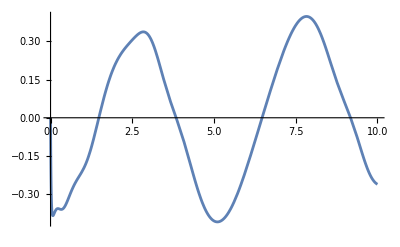

```mathematica
Plot[Tmot4[t]/.{solPathDyn},{t,0,tf}, PlotRange->All]
```

```mathematica
tf=time
```

50.

```mathematica
(*R=3;
r=0.4;
to=0;
Subscript[t, f]=Tman;
g=32.17*(12);solPathDyn=Monitor[NDSolve[{eom1n, eom2n,eom3n,eom4n,eom5,eom6,eom7,eom8,eom9,eom10,eom11,eom12,eom13,eom14,eom15,eqMn[1],eqMn[2],eqMn[3],eqMn[4],Subscript[q, 1][0]==Subscript[q, d1][0],Subscript[q, 2][0]==Subscript[q, d2][0],Subscript[q, 3][0]==Subscript[q, d3][0],Subscript[q, 4][0]==Subscript[q, d4][0],Subscript[q, 5][0]==Subscript[q, d5][0],Subscript[q, 6][0]==Subscript[q, d6][0],Subscript[q, 7][0]==Subscript[q, d7][0],Subscript[q, 8][0]==Subscript[q, d8][0],Subscript[q, 9][0]==Subscript[q, d9][0],Subscript[q, 10][0]==Subscript[q, d10][0],Subscript[q, 11][0]==Subscript[q, d11][0],Tmot1[0]==0,Tmot2[0]==0,Tmot3[0]==0,Tmot4[0]==0, p4[0]==0,p6[0]==0,p8[0]==0,p10[0]==0(*,Tmot1'[0]==0,Tmot2'[0]==0,Tmot3'[0]==0,Tmot4'[0]==0, p4'[0]==0,p6'[0]==0,p8'[0]==0,p10'[0]==0*)},{Subscript[q, 1],Subscript[q, 2],Subscript[q, 3],Subscript[q, 4],Subscript[q, 5],Subscript[q, 6],Subscript[q, 7],Subscript[q, 8],Subscript[q, 9],Subscript[q, 10],Subscript[q, 11],Tmot1,Tmot2,Tmot3,Tmot4,p4, p6,p8, p10},{t,to,Subscript[t, f]},StepMonitor:>(time=t;)(*,WorkingPrecision -> 4 *), MaxSteps->20000000,Method-> {"EquationSimplification"-> "Residual"}],ProgressIndicator[time,{to,10}]]*)
```

```mathematica
(*NDSolve[{eom1n, eom2n,eom3n,eom4n,eom5,eom6,eom7,eom8,eom9,eom10,eom11,eom12,eom13,eom14,eom15,eqMn[1]==0,eqMn[2]==0,eqMn[3]==0,eqMn[4]==0,Subscript[q, 1][0]==Subscript[q, d1][0],Subscript[q, 2][0]==Subscript[q, d2][0],Subscript[q, 3][0]==Subscript[q, d3][0],Subscript[q, 4][0]==Subscript[q, d4][0],Subscript[q, 5][0]==Subscript[q, d5][0],Subscript[q, 6][0]==Subscript[q, d6][0],Subscript[q, 7][0]==Subscript[q, d7][0],Subscript[q, 8][0]==Subscript[q, d8][0],Subscript[q, 9][0]==Subscript[q, d9][0],Subscript[q, 10][0]==Subscript[q, d10][0],Subscript[q, 11][0]==Subscript[q, d11][0],Tmot1[0]==0,Tmot2[0]==0,Tmot3[0]==0,Tmot4[0]==0, p4[0]==0,p6[0]==0,p8[0]==0,p10[0]==0},{Subscript[q, 1],Subscript[q, 2],Subscript[q, 3],Subscript[q, 4],Subscript[q, 5],Subscript[q, 6],Subscript[q, 7],Subscript[q, 8],Subscript[q, 9],Subscript[q, 10],Subscript[q, 11],Tmot1,Tmot2,Tmot3,Tmot4,p4, p6,p8, p10},{t,0,5},StepMonitor:>(time=t;)(*,WorkingPrecision -> 4 *), MaxSteps->5000,Method-> {"EquationSimplification"-> "Residual"}]*)
```

### Manipulated Plot

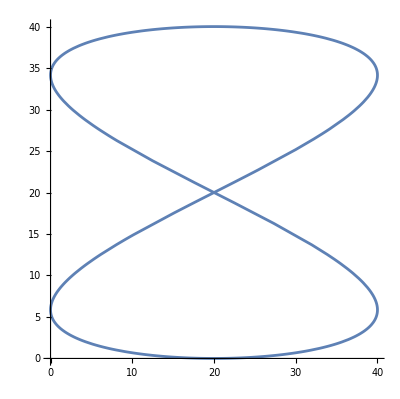

```mathematica
ParametricPlot[{Subscript[q, 1][t],Subscript[q, 2][t]}/.solPathDyn,{t,0,tf},PlotRange->All]
```

```mathematica
Manipulate[ParametricPlot[{Subscript[q, 1][t],Subscript[q, 2][t]}/.solPathDyn,{t,0,TF}],{TF,0.0001,tf,tf/10000}]
```

### Plots

```mathematica
p4pl[t_]=p4[t]/.solPathDyn;
p6pl[t_]=p6[t]/.solPathDyn;
p8pl[t_]=p8[t]/.solPathDyn;
p10pl[t_]=p10[t]/.solPathDyn;
q1pl[t_]=Subscript[q, 1][t]/.solPathDyn;
q2pl[t_]=Subscript[q, 2][t]/.solPathDyn;
q3pl[t_]=Subscript[q, 3][t]/.solPathDyn;
q4pl[t_]=Subscript[q, 4][t]/.solPathDyn;
q5pl[t_]=Subscript[q, 5][t]/.solPathDyn;
q6pl[t_]=Subscript[q, 6][t]/.solPathDyn;
q7pl[t_]=Subscript[q, 7][t]/.solPathDyn;
q8pl[t_]=Subscript[q, 8][t]/.solPathDyn;
q9pl[t_]=Subscript[q, 9][t]/.solPathDyn;
q10pl[t_]=Subscript[q, 10][t]/.solPathDyn;
q11pl[t_]=Subscript[q, 11][t]/.solPathDyn;
```

```mathematica
Po1=Plot[p4pl[t],{t,0,tf},PlotLabel->p4,PlotPoints->5000];
Po2=Plot[p6pl[t],{t,0,tf},PlotLabel->p6,PlotPoints->5000];
Po3=Plot[p8pl[t],{t,0,tf},PlotLabel->p8, PlotPoints->5000];
Po4=Plot[p10pl[t],{t,0,tf},PlotLabel->p10,PlotPoints->5000];
Pp1=Plot[q1pl[t],{t,0,tf},PlotLabel->q1,PlotPoints->5000];
Pp2=Plot[q2pl[t],{t,0,tf},PlotLabel->q2,PlotPoints->5000];
Pp3=Plot[q3pl[t],{t,0,tf},PlotLabel->q3,PlotPoints->5000];
Pp4=Plot[q4pl[t],{t,0,tf},PlotLabel->q4,PlotPoints->5000];
Pp5=Plot[q5pl[t],{t,0,tf},PlotLabel->q5,PlotPoints->5000];
Pp6=Plot[q6pl[t],{t,0,tf},PlotLabel->q6,PlotPoints->5000];
Pp7=Plot[q7pl[t],{t,0,tf},PlotLabel->q7,PlotPoints->5000];
Pp8=Plot[q8pl[t],{t,0,tf},PlotLabel->q8,PlotPoints->5000];
Pp9=Plot[q9pl[t],{t,0,tf},PlotLabel->q9,PlotPoints->5000];
Pp10=Plot[q10pl[t],{t,0,tf},PlotLabel->q10,PlotPoints->5000];
Pp11=Plot[q11pl[t],{t,0,tf},PlotLabel->q11,PlotPoints->5000];
```

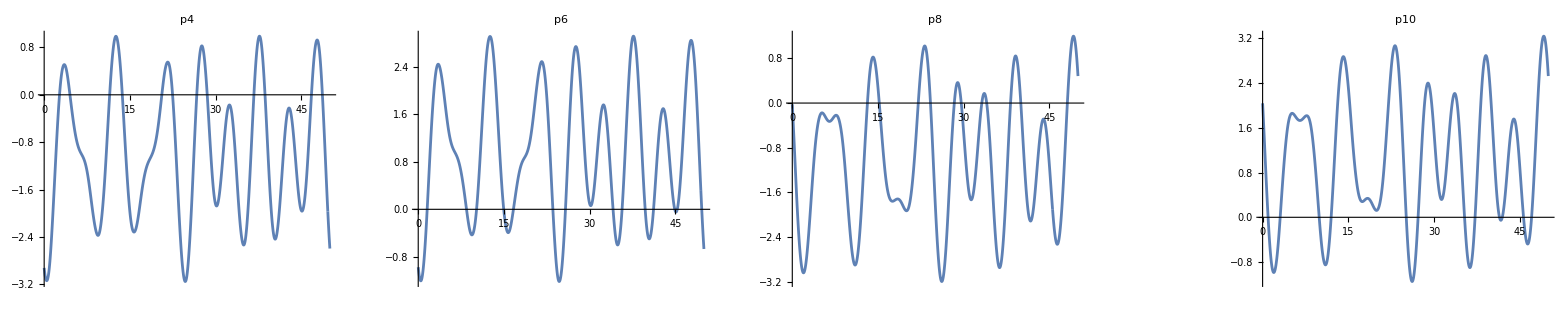

```mathematica
GraphicsRow[{Po1,Po2,Po3,,Po4}]
```

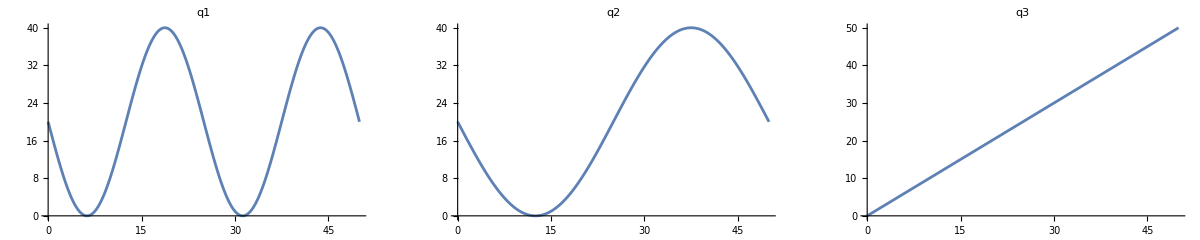

```mathematica
GraphicsRow[{Pp1,Pp2,Pp3}]
```

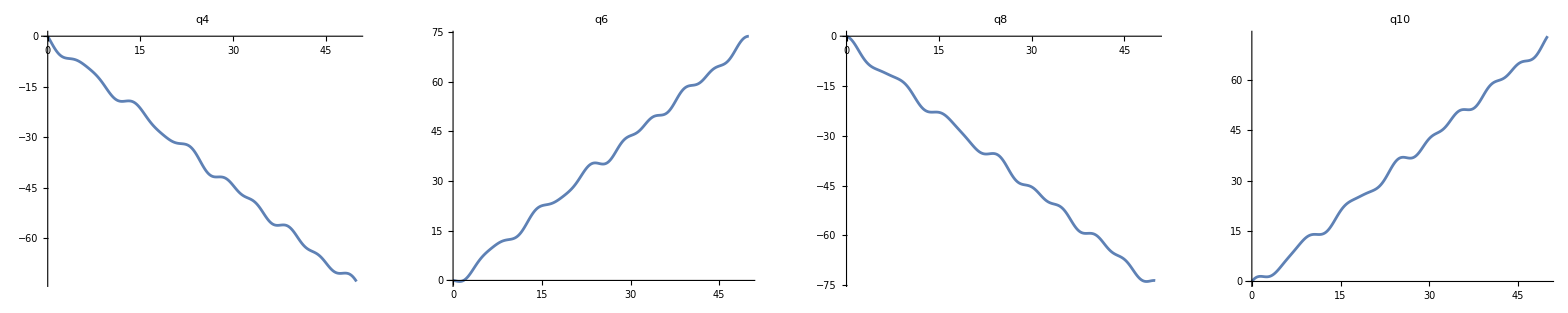

```mathematica
GraphicsRow[{Pp4,Pp6,Pp8,Pp10}]
```

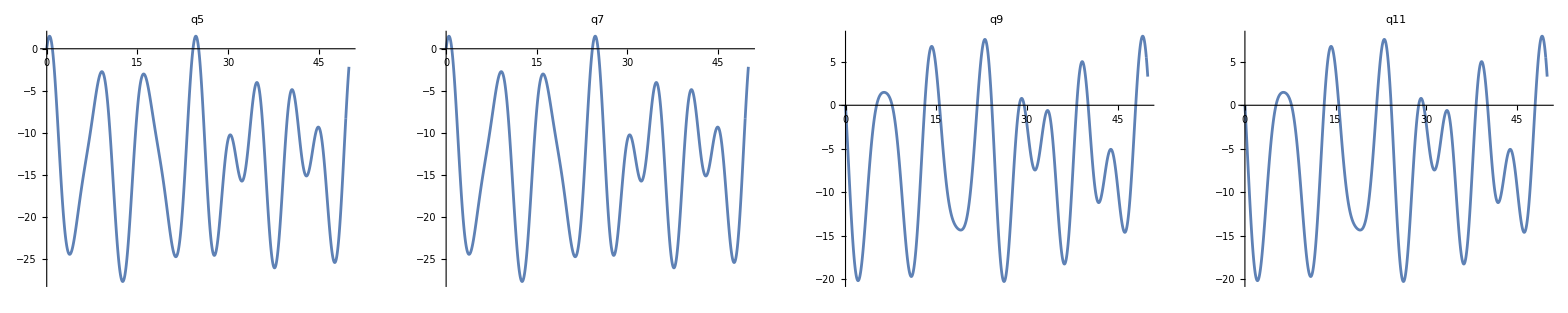

```mathematica
GraphicsRow[{Pp5,Pp7,Pp9,Pp11}]
```

### Animation of the path planned motion

```mathematica
Subscript[q, 1][t_]=Subscript[q, 1][t]/.solPathDyn//First;
Subscript[q, 2][t_]=Subscript[q, 2][t]/.solPathDyn//First;
Subscript[q, 3][t_]=Subscript[q, 3][t]/.solPathDyn//First;
Subscript[q, 4][t_]=Subscript[q, 4][t]/.solPathDyn//First;
Subscript[q, 5][t_]=Subscript[q, 5][t]/.solPathDyn//First;
Subscript[q, 6][t_]=Subscript[q, 6][t]/.solPathDyn//First;
Subscript[q, 7][t_]=Subscript[q, 7][t]/.solPathDyn//First;
Subscript[q, 8][t_]=Subscript[q, 8][t]/.solPathDyn//First;
Subscript[q, 9][t_]=Subscript[q, 9][t]/.solPathDyn//First;
Subscript[q, 10][t_]=Subscript[q, 10][t]/.solPathDyn//First;
Subscript[q, 11][t_]=Subscript[q, 11][t]/.solPathDyn//First;
```

Create composite graphic out of parts that have been rotated and translated

```mathematica
scale=40;
pathPlot=ParametricPlot3D[{Subscript[q, d1][t],Subscript[q, d2][t],Subscript[q, z][t]},{t,0,Tman},ViewPoint->{1,-1,1},ViewVertical->{0,0,1},ViewCenter->{1/2,1/2,1/2},Boxed->True,Axes->True,PlotRange->{{-0.5scale,2.5scale},{-0.5scale,2.5scale},{0,scale}},AspectRatio->1,AxesLabel->{"q_d1'[t]","q_d2'[t]","q_d3'[t]"}]
```

-Graphics3D-

```mathematica
robotGraphicPathDynAnim={
(*Base graphic*)
Translate[GeometricTransformation[baseGraphic,Transpose[rotA]],{xA,yA,zA}],

(*Wheel graphic*)
Translate[GeometricTransformation[comwheelGraphic1,Transpose[rotB]],{xB,yB,zB}],
Translate[GeometricTransformation[barrelGraphic1,Transpose[rotC]],{xC,yC,zC}],
Translate[GeometricTransformation[comwheelGraphic2,Transpose[rotD]],{xD,yD,zD}],
Translate[GeometricTransformation[comwheelGraphic3,Transpose[rotF]],{xF,yF,zF}],
Translate[GeometricTransformation[comwheelGraphic4,Transpose[rotH]],{xH,yH,zH}]
};
```

```mathematica
robotGraphicPathDynAnimT[t_]=robotGraphicPathDynAnim;
```

Loop over time

```mathematica
Animate[Show[pathPlot,Graphics3D[robotGraphicPathDynAnimT[t],ViewPoint->{1,1,1},ViewVertical->{0,0,1},ViewCenter->{1/2,1/2,1/2},Boxed->True,Axes->True,PlotRange->{{-scale,scale},{-scale,scale},{-scale,scale}},AspectRatio->1,AxesLabel->{"X","Y","Z"}]],{t,0,Tman,delT},AnimationRunning->False]
```

```mathematica
Animate[Show[Graphics3D[robotGraphicPathDynAnimT[t],ViewPoint->{1,1,1},ViewVertical->{0,0,1},ViewCenter->{1/2,1/2,1/2},Boxed->True,Axes->True,PlotRange->All,AspectRatio->1,AxesLabel->{"X","Y","Z"}]],{t,0,Tman,delT},AnimationRunning->False]
```